```mathematica
SIMSTEP4=False;
SIMSTEP6=False;
```

```mathematica
(*run everything*)
(*COMMENT=False;*)
(*some parts are not run: creation of pictures, and some other things I only needed to do once*)
COMMENT=True;
```

## position tracking for aerial slung load under unknown wind forces

## comments:

in the report I denoted the disturbances by d and D: here however they are denoted by b and B

## functions

```mathematica
(*orthognal projection to unit vector in R3*)
OP[{x1_,x2_,x3_}]=IdentityMatrix[3]-KroneckerProduct[{x1,x2,x3},{x1,x2,x3}];
(*skew matrix of vector in R3*)
Skew[{x1_,x2_,x3_}]={{0,-x3,x2},{x3,0,-x1},{-x2,x1,0}};
```

# Desired trajectory

this is not necessary for the model, only for the controller

```mathematica
(*rotation matrix*)
(*rotation matrix around 1st axis*)
Rx[θ_]:={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}};
(*rotation matrix around 2nd axis*)
Ry[θ_]:={{Cos[θ],0,Sin[θ]},{0,1,0},{-Sin[θ],0,Cos[θ]}};
(*rotation matrix around 3rd axis*)
Rz[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
(*rotation matrix*)
Rot[θ_]:=Rx[θ[[1]]].Ry[θ[[2]]].Rz[θ[[3]]]
```

```mathematica
(*position trajectory*)
(*pd[t_]:={0,0,0}*)
(*pd[t_]:={Cos[(2 π)/10 t],Sin[(2 π)/10 t],Sin[(2 π)/5 t]}*)
pd[t_]:=Rot[{25 π/180,25 π/180,0}].(1/(Sin[ωN t+ϕ]^2+1)rN {Sin[2 ωN t+ϕ]/2,Cos[ωN t+ϕ],0}+{0,0,0.5 })/.{ωN->(2 π)/If[ValueQ[FASTTRAJECTORY],8,If[ValueQ[FASTTRAJECTORY2],6,12]] ,rN-> 2,ϕ-> 0};
(*pd[t_]:=Rot[{25 π/180,25 π/180,0}].(1/(Sin[ωN t+ϕ]^2+1)rN {Sin[2 ωN t+ϕ]/2,Cos[ωN t+ϕ],0}+{0,0,0.5 })/.{ωN->(2 π)/10 ,rN-> 2,ϕ-> 0};*)
(*pd[t_]:=Rot[{25 π/180,25 π/180,0}].(1/(Sin[ωN t+ϕ]^2+1)rN {Sin[2 ωN t+ϕ]/2,Cos[ωN t+ϕ],Sin[ωN t+ϕ]}+{0,0,0.5 })/.{ωN->(2 π)/7 ,rN-> 2,ϕ-> 0};*)
(*pd[t_]:=Rot[{25 π/180,25 π/180,0}].({rN Sin[ωN t+ϕ],rN Cos[ωN t+ϕ],rN Cos[2ωN t+ϕ]}+{0,0,0.5 })/.{ωN->(2 π)/9 ,rN-> 2,ϕ-> 0};*)
```

## visualize path

```mathematica
If[
!COMMENT,
ParametricPlot3D[pd[t],{t,0,20}]
]
```

If[!COMMENT,ParametricPlot3D[pd[t],{t,0,20}]]

## trajectory needs to be C^4

```mathematica
(*velocity*)
vd[t_]:=Evaluate[pd'[t]]
(*acceleration*)
ad[t_]:=Evaluate[vd'[t]]
(*jerk*)
jd[t_]:=Evaluate[ad'[t]]
(*snap*)
sd[t_]:=Evaluate[jd'[t]]
```

## maximum of desired acceleration

```mathematica
If[
!COMMENT,
Plot[
√(#.#)&[Evaluate[pd''[t]]],
{t,0,10},
GridLines->Automatic
]
]
```

If[!COMMENT,Plot[(√(#1.#1)&)[Evaluate[pd''[t]]],{t,0,10},GridLines→Automatic]]

```mathematica
(*NMinimize[√(#.#)&[gravity{0,0,1}+{b1,b2,b3}+Evaluate[pd''[t]]/.PhysicalConstants],t∈Interval[{8,10}]]*)
ans=NMaximize[{
√(#.#)&[Evaluate[pd''[t]]]
},t
]
aBOUND=ans[[1]];
Clear[ans]
```

{1.64493,{t→-3.23569×10^-9}}

# Model/Physical parameters

note that none of the constants set next can be used by the controller

```mathematica
PhysicalConstants0=
{
gravity-> 9.81,(*acceleration due to gravity*)
l-> 1.1,(*length of cable*)
M-> 1.1,(*mass of UAV*)
m-> 0.4 (*mass of load*)
};

(*
NOTE;
later I use ϕτ and ϕτ as generic linear operators;
ϕτModel and ϕTModel are the specific ϕτ and ϕT for our model UAV-slung-load with wind;
*)
ϕTModel[{n1_,n2_,n3_}]:=(M/(m+M)){n1,n2,n3}
ϕτModel[{n1_,n2_,n3_}]:=(1/l)Skew[{n1,n2,n3}]

ϕTModelNumerical[{n1_,n2_,n3_}]:=ϕTModel[{n1,n2,n3}]/.PhysicalConstants0
ϕτModelNumerical[{n1_,n2_,n3_}]:=ϕτModel[{n1,n2,n3}]/.PhysicalConstants0



PhysicalConstants=
Join[
PhysicalConstants0,
{
(**)
ϕT1->({1,0,0}.ϕTModelNumerical[#1]&),
ϕT2->({0,1,0}.ϕTModelNumerical[#1]&),
ϕT3->({0,0,1}.ϕTModelNumerical[#1]&),
(**)
ϕτ11-> (ϕτModelNumerical[#1][[1,1]]&),
ϕτ12-> (ϕτModelNumerical[#1][[1,2]]&),
ϕτ13-> (ϕτModelNumerical[#1][[1,3]]&),
ϕτ21-> (ϕτModelNumerical[#1][[2,1]]&),
ϕτ22-> (ϕτModelNumerical[#1][[2,2]]&),
ϕτ23-> (ϕτModelNumerical[#1][[2,3]]&),
ϕτ31-> (ϕτModelNumerical[#1][[3,1]]&),
ϕτ32-> (ϕτModelNumerical[#1][[3,2]]&),
ϕτ33-> (ϕτModelNumerical[#1][[3,3]]&)
}/.PhysicalConstants0,
Thread[{w1,w2,w3}-> 0.1m gravity#/(√(#.#))&[{0.2,0,-0.2}]]/.PhysicalConstants0(*wind force on load*),
Thread[{W1,W2,W3}->  0.1M gravity#/(√(#.#))&[{0.2,0.2,0.1}]]/.PhysicalConstants0(*wind force on UAV*)
];

PhysicalConstants=Join[
PhysicalConstants,
(**)
Thread[{b1,b2,b3}->{w1,w2,w3}/m]/.PhysicalConstants,(*just for testing purposes*)
Thread[{B1,B2,B3}->{W1,W2,W3}/M-{w1,w2,w3}/m]/.PhysicalConstants(*just for testing purposes*)
];
```

```mathematica
(*test*)
```

```mathematica
If[!COMMENT,ϕT1[{1,0,0}]/.PhysicalConstants]
If[!COMMENT,ϕτ12[{0,0,1}]/.PhysicalConstants]
```

### if this condition is satisfied, desired trajectory is well defined

```mathematica
(*inf_{t≥0} \| g + b + p^(..)(t)\| >0*)
If[
!COMMENT,
Plot[
√(#.#)&[gravity{0,0,1}+{b1,b2,b3}+Evaluate[pd''[t]]/.PhysicalConstants],
{t,0,10},
GridLines->Automatic,
AxesLabel->{"Time (s)",Text[Style[ToExpression["\\inf_{t \\in \\mathbb{R}} \\left| g(t) + \\frac{w}{m} \\right|",TeXForm,HoldForm]]]}
]
]
```

### infimum of “gravity+desired acceleration”

```mathematica
If[
!COMMENT,
Plot[
√(#.#)&[gravity{0,0,1}+Evaluate[pd''[t]]/.PhysicalConstants],
{t,0,12},
GridLines->Automatic
]
]
```

```mathematica
(*NMinimize[√(#.#)&[gravity{0,0,1}+{b1,b2,b3}+Evaluate[pd''[t]]/.PhysicalConstants],t∈Interval[{8,10}]]*)
ans=NMinimize[{
√(#.#)&[gravity{0,0,1}+Evaluate[pd''[t]]/.PhysicalConstants],
0≤ t≤ 12
},t
]
gBOUND=ans[[1]];
Clear[ans]
```

{8.06613,{t→5.77875}}

### better use the gBound than the aBound

```mathematica
gBOUND-(gravity-aBOUND)/.PhysicalConstants
```

-0.0989401

```mathematica
(*NMinimize[√(#.#)&[gravity{0,0,1}+{b1,b2,b3}+Evaluate[pd''[t]]/.PhysicalConstants],t∈Interval[{8,10}]]*)
ans=NMaximize[{
√(#.#)&[Evaluate[pd''[t]]]
},t
]
aBOUND=ans[[1]];
Clear[ans]
```

{6.57974,{t→-7.72289×10^-9}}

## excitation criterion

```mathematica
If[
!COMMENT,
Plot[
√(#.#)&[Skew[#1/(√(#1.#1))].(#2/(√(#1.#1)))&[gravity+Evaluate[pd''[t]] -{b1,b2,b3},Evaluate[pd'''[t]]]/.PhysicalConstants],
{t,0,12},
GridLines->Automatic
]
]
```

```mathematica
NIntegrate[√(#.#)&[Skew[#1/(√(#1.#1))].(#2/(√(#1.#1)))&[gravity+Evaluate[pd''[t]] -{b1,b2,b3},Evaluate[pd'''[t]]]/.PhysicalConstants],{t,0,12}]/12
```

0.0555066

```mathematica
(*NIntegrate[√(#.#)&[Skew[#1/(√(#1.#1))].#2/(√(#1.#1))&[gravity+Evaluate[pd''[t]] -{b1,b2,b3},Evaluate[pd'''[t]]]/.PhysicalConstants],{t,0,8}]/8
(*0.18811587668411547*)*)
```

0.188116

```mathematica
(*NIntegrate[√(#.#)&[Skew[#1/(√(#1.#1))].#2/(√(#1.#1))&[gravity+Evaluate[pd''[t]] -{b1,b2,b3},Evaluate[pd'''[t]]]/.PhysicalConstants],{t,0,6}]/6*)
(*0.45056263086673815*)
```

# Controller parameters

## double integrator control

### parameters related to bounded control of a double integrator

```mathematica
DIGains={
(*horizontal*)
kph->1.4^2,(*proportional gain for position control*)
kdh->2 1.4 0.7, (*derivative gain for position control*)
(**)
σph-> 1.5,(*position error saturation*)
σvh->2,(*velocity error saturation*)
βh->0.98, (*parameter in Lyapunov function that guarantees that V >0  and V̇ <0*)
(*vertical*)
(*kp->1.5^2,(*proportional gain for position control*)
kd->2 1.5 0.8, (*derivative gain for position control*)*)
kpz->1.5^2,(*proportional gain for position control*)
kdz->2 1.5 0.7, (*derivative gain for position control*)
(**)
σpz-> 1.5,(*position error saturation*)
σvz->2,(*velocity error saturation*)
βz->1.06 (*parameter in Lyapunov function that guarantees that V >0  and V̇ <0*)
};
```

#### condition that must be satisfied by β parameter

condition that must be satisfied by β parameter

```mathematica
(*βBound*)
Min[√kpz,kdz/(1+kdz^2/(2 kpz))]/.DIGains
Min[√kph,kdh/(1+kdh^2/(2 kph))]/.DIGains
```

1.06061

0.989899

#### β < kv/(1+kv^2/(4 kp))≤ min(√kp,kv/(1+kv^2/(4 kp))) note that β can be defined in simpler manner

```mathematica
Simplify[√kp-ωn/.{kv-> 2 ξ ωn,kp-> ωn^2},ωn>0]
Simplify[kv/(1+kv^2/(4 kp))-1/(1+(ξ-1)^2/(2 ξ))ωn/.{kv-> 2 ξ ωn,kp-> ωn^2}]
```

0

0

```mathematica
(*condition that must be satisfied by β parameter*)
DICondition[kp_,kd_,β_]:=β<Min[√kp,kd/(1+kd^2/(2 kp))]
```

```mathematica
(*check that condition is satisfied*)
(*vertical gains*)
DICondition[kpz,kdz,βz]/.DIGains
(*horizontal gains*)
DICondition[kph,kdh,βh]/.DIGains
```

True

True

#### bound of bounded controller

```mathematica
(*option 1*)
(*uBOUND=√((kph σph+kdh σvh)^2+(kpz σpz+kdz σvz)^2)/.DIGains*)
(*option 2*)
uBOUND=√((kph σph √(1+((kdh σvh)/(kph σph))^2))^2+(kpz σpz √(1+((kdz σvz)/(kpz σpz))^2))^2)/.DIGains
```

7.2829

### control law and companion Lyapunov function

```mathematica
(*uDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]:={-kp p1-kd v1,-kp p2-kd v2,-kp p3-kd v3}/.DIGains;
VDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]:=( #1.#1+2 kd/(2 (kd^2+kp)) #1.#2+(kd^2+2 kp)/(2 kd^2 kp+2 kp^2) #2.#2)&[{p1,p2,p3},{v1,v2,v3}]/.DIGains;*)

(*uDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]:=-kp#1/(√(1+(#1.#1)/σp^2))-kd#2/(√(1+(#2.#2)/σv^2))&[{p1,p2,p3},{v1,v2,v3}]/.DIGains;
VDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]:=kp σp^2( √((#1.#1)/σp^2+1)-1)  +β (#1/(√(1+(#1.#1)/σp^2))).(#2/(√(1+(#2.#2)/σv^2)))+(#2.#2)/2&[{p1,p2,p3},{v1,v2,v3}]/.DIGains;*)
```

option 1

```mathematica
σσ[x_,σ_]:=x/(√(1+(x.x)/σ^2))
uDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=-kp σσ[p,σp]-kd σσ[v,σd];
VDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=kp σp^2( √((p.p)/σp^2+1)-1)  +β σσ[p,σp].σσ[v,σd]+(v.v)/2;

JoinAs[A11_,A12_,A21_,A22_]:=Join[Join[A11,A12,2],Join[A21,A22,2]]
Ws[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=1/(√(1+(v.v)/σd^2))JoinAs[
kp β √(1+(v.v)/σd^2)D[σσ[v,σd],{v}],
1/2 β kd D[σσ[v,σd],{v}],1/2 β kd D[σσ[v,σd],{v}],
kd IdentityMatrix[Length[p]]-β D[σσ[p,σp],{p}]
]
WDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=-#1.Ws[p,v,{kp,σp,kd,σd,β}].#1&[Join[σσ[p,σp],v]];
```

```mathematica
(*check that indeed V̇(p,v)=W(p,v)*)
error[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=WDIA[p,v,{kp,σp,kd,σd,β}]-D[VDIA[p,v,{kp,σp,kd,σd,β}],{Join[p,v]}].Join[v,uDIA[p,v,{kp,σp,kd,σd,β}]]
error[{p1,p2,p3},{v1,v2,v3},{kp,σp,kd,σd,β}]//Simplify
```

0

```mathematica
uDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[Join[uDIA[{p1,p2},{v1,v2},{kph,σph,kdh,σvh,βh}],uDIA[{p3},{v3},{kpz,σpz,kdz,σvz,βz}]]/.DIGains];
VDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[VDIA[{p1,p2},{v1,v2},{kph,σph,kdh,σvh,βh}]+VDIA[{p3},{v3},{kpz,σpz,kdz,σvz,βz}]/.DIGains];
WDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[WDIA[{p1,p2},{v1,v2},{kph,σph,kdh,σvh,βh}]+WDIA[{p3},{v3},{kpz,σpz,kdz,σvz,βz}]/.DIGains];
```

```mathematica
(*test*)
If[!COMMENT,uDIChosen[{2,2,2},{1,1,2}]]
If[!COMMENT,VDIChosen[{2,2,2},{1,1,2}]]
If[!COMMENT,WDIChosen[{2,2,2},{1,1,2}]]
```

option 2

```mathematica
σσ[x_,σ_]:=x/(√(1+(x.x)/σ^2))
uDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=-kp 1/(√(1+(v.v)/σd^2))σσ[p,σp]-kd σσ[v,σd];
VDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=kp σp^2( √((p.p)/σp^2+1)-1)  +β σσ[p,σp].σσ[v,σd]+1/3 σd^2 ((√(1+(v.v)/σd^2))^3 -1);

JoinAs[A11_,A12_,A21_,A22_]:=Join[Join[A11,A12,2],Join[A21,A22,2]]
Ws[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=1/(√(1+(v.v)/σd^2))JoinAs[
kp β D[σσ[v,σd],{v}],
1/2 β kd D[σσ[v,σd],{v}],1/2 β kd D[σσ[v,σd],{v}],
√(1+(v.v)/σd^2)kd IdentityMatrix[Length[p]]-β D[σσ[p,σp],{p}]
]
WDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=-#1.Ws[p,v,{kp,σp,kd,σd,β}].#1&[Join[σσ[p,σp],v]];
```

```mathematica
(*check that indeed V̇(p,v)=W(p,v)*)
error[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=WDIA[p,v,{kp,σp,kd,σd,β}]-D[VDIA[p,v,{kp,σp,kd,σd,β}],{Join[p,v]}].Join[v,uDIA[p,v,{kp,σp,kd,σd,β}]]
error[{p1,p2,p3},{v1,v2,v3},{kp,σp,kd,σd,β}]//Simplify
```

0

```mathematica
uDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[Join[uDIA[{p1,p2},{v1,v2},{kph,σph,kdh,σvh,βh}],uDIA[{p3},{v3},{kpz,σpz,kdz,σvz,βz}]]/.DIGains];
VDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[VDIA[{p1,p2},{v1,v2},{kph,σph,kdh,σvh,βh}]+VDIA[{p3},{v3},{kpz,σpz,kdz,σvz,βz}]/.DIGains];
WDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[WDIA[{p1,p2},{v1,v2},{kph,σph,kdh,σvh,βh}]+WDIA[{p3},{v3},{kpz,σpz,kdz,σvz,βz}]/.DIGains];
```

```mathematica
(*test*)
If[!COMMENT,uDIChosen[{2,2,2},{1,1,2}]]
If[!COMMENT,VDIChosen[{2,2,2},{1,1,2}]]
If[!COMMENT,WDIChosen[{2,2,2},{1,1,2}]]
```

### necessary derivatives of both the functions above

```mathematica
d1uDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[D[uDIChosen[#1,#2],{#1}]&[{p1,p2,p3},{v1,v2,v3}]]//Simplify;
d2uDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[D[uDIChosen[#1,#2],{#2}]&[{p1,p2,p3},{v1,v2,v3}]]//Simplify;

d1d1uDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[D[d1uDIChosen[#1,#2],{#1}]&[{p1,p2,p3},{v1,v2,v3}]]//Simplify;
d2d1uDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[D[d1uDIChosen[#1,#2],{#2}]&[{p1,p2,p3},{v1,v2,v3}]]//Simplify;

d1d2uDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[D[d2uDIChosen[#1,#2],{#1}]&[{p1,p2,p3},{v1,v2,v3}]]//Simplify;
d2d2uDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[D[d2uDIChosen[#1,#2],{#2}]&[{p1,p2,p3},{v1,v2,v3}]]//Simplify;

d1VDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[D[VDIChosen[#1,#2],{#1}]&[{p1,p2,p3},{v1,v2,v3}]]//Simplify;
d2VDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[D[VDIChosen[#1,#2],{#2}]&[{p1,p2,p3},{v1,v2,v3}]]//Simplify;

d1d2VDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[D[d2VDIChosen[#1,#2],{#1}]&[{p1,p2,p3},{v1,v2,v3}]]//Simplify;
d2d2VDIChosen[{p1_,p2_,p3_},{v1_,v2_,v3_}]=Evaluate[D[d2VDIChosen[#1,#2],{#2}]&[{p1,p2,p3},{v1,v2,v3}]]//Simplify;
```

```mathematica
(*small test*)
If[!COMMENT,d2d2uDIChosen[{1,2,3},{4,5,6}]]
If[!COMMENT,d2d2VDIChosen[{1,2,3},{4,5,6}]]
```

## parameters that relate to backstepping procedure

```mathematica
ControlParameters=Join[
DIGains,
{
(*values that determine when to "start" integrating and backstepping*)
Subscript[V, 1,0]->If[ValueQ[ESTIMATESENSITIVITY],2, If[ValueQ[ESTIMATESENSITIVITY2],20, If[ValueQ[ESTIMATESENSITIVITY3],200,1.5]]],(*Lyapunov function at step 1 "threshold"*)
Subscript[V, 2,0]->If[ValueQ[ESTIMATESENSITIVITY],2, If[ValueQ[ESTIMATESENSITIVITY2],20,If[ValueQ[ESTIMATESENSITIVITY3],200,1.5]]],(*Lyapunov function at step 2 "threshold"*)
(**)
γθ-> 5,(*weight of angular position in Lyapunov function*)
kpθ-> 3,(*gain of angular position in control law*)
(**)
γω->10,(*weight of angular velocity in Lyapunov function*)
kpω-> 5(*gain of angular velocity in control law*),
(**)
gravity-> (gravity/.PhysicalConstants)+0,(*acceleration due to gravity*)
l-> (l/.PhysicalConstants)+If[ValueQ[SIMNOTPERFECTMODEL],0.1,0],(*cable length as known by controller*)
M-> (M/.PhysicalConstants)+If[ValueQ[SIMNOTPERFECTMODEL],0,0],(*UAV weight as known by controller*)
m-> (m/.PhysicalConstants)+If[ValueQ[SIMNOTPERFECTMODEL],0.1,0],(*load weight as known by controller*)
(**)
kpUAV-> 25(*proportional gain for attitude control of UAV*),
kdUAV-> 2 1.3 √25(*derivative gain for attitude control of UAV*)
}
];
```

### how to choose V_(1,0) and V_(2,0)

```mathematica
(*how to choose Subscript[V, 1,0]*)
VDIChosen[{0.5,0.5,0.5},{0.5,0.5,0.5}]
(*how to choose Subscript[V, 2,0]*)
Subscript[V, 1,0] Log[(2 Subscript[V, 1,0])/Subscript[V, 1,0]]+γθ(1-Cos[30 π/180])/.{Subscript[V, 1,0]-> VDIChosen[{0.5,0.5,0.5},{0.5,0.5,0.5}]}/.ControlParameters//N
```

1.78564

1.90758

## other necessary parameters

### This is the ϕT and ϕτ defined later in the model: they also need to be known by the controller

```mathematica
(*ϕτModel[{n1_,n2_,n3_}]:=1/L Skew[{n1,n2,n3}]*)
(*ϕTModel[{n1_,n2_,n3_}]:=M/(m+M){n1,n2,n3}*)

(*these are not necessarily equal to the model ones*)
ϕTController[{n1_,n2_,n3_}]:=M/(m+M){n1,n2,n3}
ϕτController[{n1_,n2_,n3_}]:=1/l Skew[{n1,n2,n3}]

ϕTControllerNumerical[{n1_,n2_,n3_}]:=ϕTController[{n1,n2,n3}]/.ControlParameters
ϕτControllerNumerical[{n1_,n2_,n3_}]:=ϕτController[{n1,n2,n3}]/.ControlParameters
```

### combining all the controller parameters

```mathematica
Controllers:=Join[
{
uDI1->({1,0,0}.uDIChosen[#1,#2]&),
uDI2->({0,1,0}.uDIChosen[#1,#2]&),
uDI3->({0,0,1}.uDIChosen[#1,#2]&),
V1->(VDIChosen[#2[[1;;3]],#2[[4;;6]]]&),
(**)
g1->(-{1,0,0}.Evaluate[pd''[#]]&),
g2->(-{0,1,0}.Evaluate[pd''[#]]&),
g3->(-{0,0,1}.Evaluate[pd''[#]]+(gravity/.ControlParameters)&),
(**)
ϕT1->({1,0,0}.ϕTControllerNumerical[#1]&),
ϕT2->({0,1,0}.ϕTControllerNumerical[#1]&),
ϕT3->({0,0,1}.ϕTControllerNumerical[#1]&),
(**)
ϕτ11-> (ϕτControllerNumerical[#1][[1,1]]&),
ϕτ12-> (ϕτControllerNumerical[#1][[1,2]]&),
ϕτ13-> (ϕτControllerNumerical[#1][[1,3]]&),
ϕτ21-> (ϕτControllerNumerical[#1][[2,1]]&),
ϕτ22-> (ϕτControllerNumerical[#1][[2,2]]&),
ϕτ23-> (ϕτControllerNumerical[#1][[2,3]]&),
ϕτ31-> (ϕτControllerNumerical[#1][[3,1]]&),
ϕτ32-> (ϕτControllerNumerical[#1][[3,2]]&),
ϕτ33-> (ϕτControllerNumerical[#1][[3,3]]&)
}
,
ControlParameters
]
```

```mathematica
(*small test*)
If[!COMMENT,uDI1[{1,2,3},{4,5,6}]/.Controllers]
If[!COMMENT,ϕT1[{1,0,0}]/.Controllers]
If[!COMMENT,ϕτ12[{0,0,1}]/.Controllers]
```

-2.66297

0.733333

-0.909091

## n^th differentiable update law (for estimators)

The projector operator is “sufficiently smooth”, but because it is defined with an “if” condition, it makes the differentiation of the projector complicated and it makes the symbolic calculations really slow later on. That is the main reason for the next auxiliary definitions

### auxiliary definitions, before Projector is defined

```mathematica
(*EstimatorProj2[bdot_,b_,{θ0_,ϵ_,δ_,n_}]:=bdot-((b.b-θ0^2)^(n+1) (1/2 b.bdot+√((1/2 b.bdot)^2+δ^2)))/(4(ϵ^2+2ϵ θ0)^(n+1)θ0^2)b*)
(*EstimatorProj2[bdot_,b_,{θ0_,ϵ_,δ_,n_}]:=bdot-((Exp[n(#-1)/#])&[(b.b-θ0^2)/((θ0+ϵ)^2-θ0^2)])(((#.bdot+√((#.bdot)^2+δ^2))/2#)&[b/θ0])*)
EstimatorProj2[bdot_,b_,{θ0_,ϵ_,δ_,n_}]:=bdot-Exp[n(1-1/((b.b-θ0^2)/((θ0+ϵ)^2-θ0^2)))](((b/θ0).bdot+√(((b/θ0).bdot)^2+δ^2))/2 b/θ0)
d1EstimatorProj2[{bdot1_,bdot2_,bdot3_},{b1_,b2_,b3_},{θ0_,ϵ_,δ_,n_}]=Simplify[
Evaluate[
D[EstimatorProj2[{bdot1,bdot2,bdot3},{b1,b2,b3},{θ0,ϵ,δ,n}],{{bdot1,bdot2,bdot3}}]
]
];
d2EstimatorProj2[{bdot1_,bdot2_,bdot3_},{b1_,b2_,b3_},{θ0_,ϵ_,δ_,n_}]=Simplify[
Evaluate[D[EstimatorProj2[{bdot1,bdot2,bdot3},{b1,b2,b3},{θ0,ϵ,δ,n}],{{b1,b2,b3}}]
]
];
```

### definition of Proj

```mathematica
EstimatorProj[bdot_,b_,{θ0_,ϵ_,δ_,n_}]:=If[(b.b-θ0^2)≤ 0,bdot,EstimatorProj2[bdot,b,{θ0,ϵ,δ,n}]]
```

### necessary derivatives

```mathematica
d1EstimatorProj[bdot_,b_,{θ0_,ϵ_,δ_,n_}]:=If[(b.b-θ0^2)≤ 0,IdentityMatrix[Length[bdot]],d1EstimatorProj2[bdot,b,{θ0,ϵ,δ,n}]]
d2EstimatorProj[bdot_,b_,{θ0_,ϵ_,δ_,n_}]:=If[(b.b-θ0^2)≤ 0,ConstantArray[0,{Length[bdot],Length[bdot]}],d2EstimatorProj2[bdot,b,{θ0,ϵ,δ,n}]]
(*test*)
d1EstimatorProj[RandomReal[{-2,2},3],RandomReal[{-2,2},3],{1,1,1,3}]
d2EstimatorProj[RandomReal[{-2,2},3],RandomReal[{-2,2},3],{1,1,1,3}]
```

{{0.949002,-0.426869,0.252507},{-0.426869,-2.57301,2.11355},{0.252507,2.11355,-0.250234}}

{{-8.56977,-0.172389,-1.197},{-4.45127,-1.0952,-0.703309},{-1.204,-0.027397,-1.18415}}

### smoothness property

#### test n=1 (this was only necessary to check with projector that was not smooth)

```mathematica
(*(*derivative at boundary*)
If[!COMMENT,
Simplify[
D[EstimatorProj2[{b1dot,b2dot},{b1,b2},{θ0,ϵ,δ,n}],{{b1,b2},1}]/.Thread[{b1,b2}-> θ0{1,0}]
]/.{n-> 1}
]
If[!COMMENT,
Simplify[
D[EstimatorProj2[{b1dot,b2dot},{b1,b2},{θ0,ϵ,δ,n}],{{b1,b2},2}]/.Thread[{b1,b2}-> θ0{1,0}]
]/.{n-> 1}
]*)
```

#### test n=2 (this was only necessary to check with projector that was not smooth)

```mathematica
(*(*derivative at boundary*)
If[!COMMENT,
Simplify[
D[EstimatorProj2[{b1dot,b2dot},{b1,b2},{θ0,ϵ,δ,n}],{{b1,b2},1}]/.Thread[{b1,b2}-> θ0{1,0}]
]/.{n-> 2}
]
If[!COMMENT,
Simplify[
D[EstimatorProj2[{b1dot,b2dot},{b1,b2},{θ0,ϵ,δ,n}],{{b1,b2},2}]/.Thread[{b1,b2}-> θ0{1,0}]
]/.{n-> 2}
]
(*it takes a bit of time, so i have suppressed this: but eventually it says indeterminate*)
(*Simplify[
D[EstimatorProj2[{b1dot,b2dot},{b1,b2},{θ0,ϵ,δ,n}],{{b1,b2},3}]/.Thread[{b1,b2}-> θ0{1,0}]
]/.{n-> 2}*)*)
```

### property that involves inner product: inner product > 0 provided that real b lies inside the Ball(0.9)

```mathematica
If[!COMMENT,
Plot3D[
({b1,b2}-{b1d,b2d}).EstimatorProj[{μ1,μ2},{b1d,b2d},{0.5,0.5,8,3}]-({b1,b2}-{b1d,b2d}).{μ1,μ2}/.Thread[{μ1,μ2}-> {0.1,0.1}]/.Thread[{b1d,b2d}-> {0.9,0}],
{b1,-1,1},
{b2,-1,1},
PlotRange->{0,5},
RegionFunction->Function[{x,y},x^2+y^2≤ (1)^2]
]
]
```

-Graphics3D-

### Stream plot is doing something funny, where there is a stream line exiting the ball, but it shouldn’t

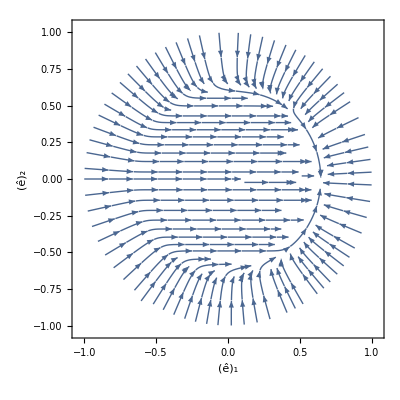

```mathematica
StreamPlot[
EstimatorProj[{0.1,0},{b1d,b2d},{#/2,#/2,5,1}],
{b1d,-#,#},
{b2d,-#,#},
StreamPoints->80,
RegionFunction->Function[{x,y},x^2+y^2≤(#)^2],
FrameLabel->{
Text[Style[ToExpression["\\hat{e}_{1}",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\hat{e}_{2}",TeXForm,HoldForm]]]
}
]&[1]
If[!COMMENT,Export[NotebookDirectory[]<>"./figures/estimator_vector_field.pdf",%];]
```

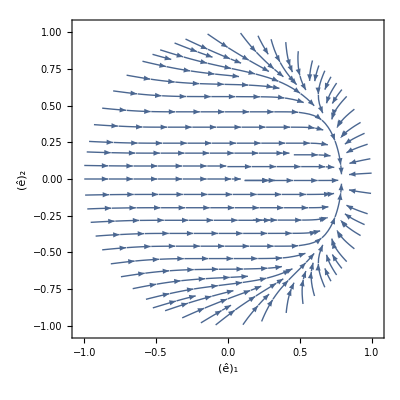

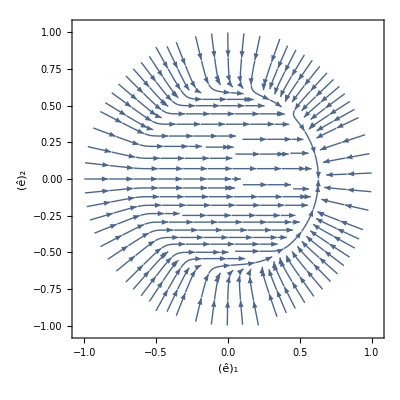

```mathematica
StreamPlot[
EstimatorProj[{0.1,0},{b1d,b2d},{#/2,#/2,0.1,1}],
{b1d,-#,#},
{b2d,-#,#},
StreamPoints->80,
RegionFunction->Function[{x,y},x^2+y^2≤(#)^2],
FrameLabel->{
Text[Style[ToExpression["\\hat{e}_{1}",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\hat{e}_{2}",TeXForm,HoldForm]]]
}
]&[1]
If[!COMMENT,Export[NotebookDirectory[]<>"./figures/estimator_vector_field1.pdf",%];]
StreamPlot[
EstimatorProj[{0.1,0},{b1d,b2d},{#/2,#/2,10,1}],
{b1d,-#,#},
{b2d,-#,#},
StreamPoints->80,
RegionFunction->Function[{x,y},x^2+y^2≤(#)^2],
FrameLabel->{
Text[Style[ToExpression["\\hat{e}_{1}",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\hat{e}_{2}",TeXForm,HoldForm]]]
}
]&[1]
If[!COMMENT,Export[NotebookDirectory[]<>"./figures/estimator_vector_field2.pdf",%];]
```

## estimator gains

### estimator parameters (may be merged with controller parameters)

```mathematica
(*too fast for fully-actuated*)
(*EstimatorsParameters={
kibT-> {3.5,3.5,3.5},θ0bT->0.4 ,ϵbT-> 0.1,δbT-> 1,nbT-> 1,
kiBT->{7,7,7},θ0BT->0.4 ,ϵBT-> 0.1,δBT-> 1,nBT-> 1,
kibτ-> 0.05,θ0bτ->0.4,ϵbτ-> 0.1,δbτ-> 1,nbτ-> 1,
kiBτ-> 0.05,θ0Bτ->0.4,ϵBτ-> 0.2,δBτ-> 1,nBτ-> 1
};*)

(* for model mismatch: θ0bT = 0.4 and θ0BT = 0.4 are too small*)
EstimatorsParameters={
kibT-> {3,3,3},θ0bT->If[ValueQ[SIMNOTPERFECTMODEL],2.4,1.2] ,ϵbT-> 0.3,δbT-> 1,nbT-> 1,
kiBT->{10,10,10},θ0BT->If[ValueQ[SIMNOTPERFECTMODEL],3,1.5] ,ϵBT-> 0.3,δBT-> 1,nBT-> 1,
kibτ-> 0.05,θ0bτ->If[ValueQ[SIMNOTPERFECTMODEL],2.4,1.2],ϵbτ-> 0.3,δbτ-> 1,nbτ-> 1,
kiBτ-> 0.05,θ0Bτ->If[ValueQ[SIMNOTPERFECTMODEL],3,1.5],ϵBτ-> 0.3,δBτ-> 1,nBτ-> 1
};
```

### these are the components of the update laws, which will depend on functions to be defined later on

```mathematica
Estimators:=Join[
{
XbT1->({1,0,0}.EstimatorProj[kibT[[1]] XbTChosenFast[#1,#2],#2,{θ0bT,ϵbT,δbT,nbT}]&),
XbT2->({0,1,0}.EstimatorProj[kibT[[2]] XbTChosenFast[#1,#2],#2,{θ0bT,ϵbT,δbT,nbT}]&),
XbT3->({0,0,1}.EstimatorProj[kibT[[3]] XbTChosenFast[#1,#2],#2,{θ0bT,ϵbT,δbT,nbT}]&),
(**)
XBT1->({1,0,0}.EstimatorProj[kiBT[[1]] XBTChosenFast[#1,#2],#2,{θ0BT,ϵBT,δBT,nBT}]&),
XBT2->({0,1,0}.EstimatorProj[kiBT[[2]] XBTChosenFast[#1,#2],#2,{θ0BT,ϵBT,δBT,nBT}]&),
XBT3->({0,0,1}.EstimatorProj[kiBT[[3]] XBTChosenFast[#1,#2],#2,{θ0BT,ϵBT,δBT,nBT}]&),
(**)
Xbτ1->({1,0,0}.EstimatorProj[kibτ XbτChosenFast[#1,#2],#2,{θ0bτ,ϵbτ,δbτ,nbτ}]&),
Xbτ2->({0,1,0}.EstimatorProj[kibτ XbτChosenFast[#1,#2],#2,{θ0bτ,ϵbτ,δbτ,nbτ}]&),
Xbτ3->({0,0,1}.EstimatorProj[kibτ XbτChosenFast[#1,#2],#2,{θ0bτ,ϵbτ,δbτ,nbτ}]&),
(**)
XBτ1->({1,0,0}.EstimatorProj[kiBτ XBτChosenFast[#1,#2],#2,{θ0Bτ,ϵBτ,δBτ,nBτ}]&),
XBτ2->({0,1,0}.EstimatorProj[kiBτ XBτChosenFast[#1,#2],#2,{θ0Bτ,ϵBτ,δBτ,nBτ}]&),
XBτ3->({0,0,1}.EstimatorProj[kiBτ XBτChosenFast[#1,#2],#2,{θ0Bτ,ϵBτ,δBτ,nBτ}]&)
}/.EstimatorsParameters/.ControlParameters(*chosen update laws may depend on control parameters*)
,
EstimatorsParameters
]
```

```mathematica
(*test*)
If[!COMMENT,XbT1[{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{1,1,1}]/.Estimators]
```

-0.673883 ({0.833333,0.833333,0.833333}.(2 XbTChosenFast[{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{1,1,1}])+√(1+({0.833333,0.833333,0.833333}.(2 XbTChosenFast[{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{1,1,1}]))^2))+2 XbTChosenFast[{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{1,1,1}]

## check θ0bT, θ0BT, θ0bτ, θ0Bτ

```mathematica
(*these ratios need to be bigger than 1*)
(θ0bT/.EstimatorsParameters)/(√(#.#)&[{w1,w2,w3}/m]/.PhysicalConstants)
(θ0BT/.EstimatorsParameters)/(√(#.#)&[{W1,W2,W3}/M-{w1,w2,w3}/m]/.PhysicalConstants)
```

1.22324

1.23673

```mathematica
(θ0bT/.EstimatorsParameters)>(√(#.#)&[{w1,w2,w3}/m]/.PhysicalConstants)
(θ0BT/.EstimatorsParameters)>(√(#.#)&[{W1,W2,W3}/M-{w1,w2,w3}/m]/.PhysicalConstants)
(θ0bτ/.EstimatorsParameters)>(√(#.#)&[{w1,w2,w3}/m]/.PhysicalConstants)
(θ0Bτ/.EstimatorsParameters)>(√(#.#)&[{W1,W2,W3}/M-{w1,w2,w3}/m]/.PhysicalConstants)
```

True

True

True

«1 more identical outputs»

## merge controller parameters, and estimator parameters

```mathematica
ControllersWithEstimators=Join[Controllers,Estimators];
```

## check conditions that guarantee all will be well defined

### how much can be used for bounded double integrator

```mathematica
gBOUND-(θ0bT+ϵbT)/.Estimators
```

7.52802

### if positive, everything will be well defined

```mathematica
(* maximum norm (θ0bT+ϵbT)/.Estimators*)
gBOUND-(uBOUND+(θ0bT+ϵbT))/.Estimators
```

0.245121

### condition below not satisfied because it is too restrictive

```mathematica
gravity-(aBOUND+uBOUND+(θ0bT+ϵbT))/.ControllersWithEstimators
```

-0.617834

# Angular and Torque control

```mathematica
AngularVelocity[n_,{y0d_,y1d_},{V_,dV_},{k_,γ_,V0_}]:=-k Skew[y0d/(√(y0d.y0d))].n+OP[n].(Skew[y0d/(y0d.y0d)].y1d+1/γ(1+V/V0)^-1 dV)
```

```mathematica
W1[n_,{y0d_,y1d_},{V_,dV_},{k_,γ_,V0_},ω_]:=D[V0 Log[(V+V0)/V0]+γ(1-n.(y0d/(√(y0d.y0d)))),{Join[{V},n,y0d]}].Join[{W+dV.Skew[n].(y0d/(√(y0d.y0d)))},Skew[ω].n,y1d]
```

```mathematica
W2[n_,{y0d_,y1d_},{V_,dV_},{k_,γ_,V0_}]:=(1+V/V0)^-1 W-k γ #.# &[Skew[n].(y0d/(√(y0d.y0d)))]
```

```mathematica
error[n_,{y0d_,y1d_},{V_,dV_},{k_,γ_,V0_}]:=W2[n,{y0d,y1d},{V,dV},{k,γ,V0}]-W1[n,{y0d,y1d},{V,dV},{k,γ,V0},AngularVelocity[n,{y0d,y1d},{V,dV},{k,γ,V0}]]
```

```mathematica
error[{n1,n2,n3},{{y0d1,y0d2,y0d3},{y1d1,y1d2,y1d3}},{V,{dV1,Subscript[dV, 2],dV3}},{k,γ,V0}]//Simplify
```

0

```mathematica
AngularAcceleration[ω_,{ω0d_,ω1d_},{V_,dV_},{k_,γ_,V0_}]:=ω1d-k (ω-ω0d)-1/γ(1+V/V0)^-1 dV
W1[ω_,{ω0d_,ω1d_},{V_,dV_},{k_,γ_,V0_},τ_]:=D[V0 Log[(V+V0)/V0]+γ(#.#)/2&[ω-ω0d],{Join[{V},ω,ω0d]}].Join[{W+dV.(ω-ω0d)},τ,ω1d]
W2[ω_,{ω0d_,ω1d_},{V_,dV_},{k_,γ_,V0_}]:=(1+V/V0)^-1 W-k γ #.# &[ω-ω0d]
error[ω_,{ω0d_,ω1d_},{V_,dV_},{k_,γ_,V0_}]:=W2[ω,{ω0d,ω1d},{V,dV},{k,γ,V0}]-W1[ω,{ω0d,ω1d},{V,dV},{k,γ,V0},AngularAcceleration[ω,{ω0d,ω1d},{V,dV},{k,γ,V0}]]
error[{ω1,ω2,ω3},{{ω0d1,ω0d2,ω0d3},{ω1d1,ω1d2,ω1d3}},{V,{dV1,Subscript[dV, 2],dV3}},{k,γ,V0}]//Simplify
```

0

```mathematica
Clear[W1,W2]
```

# Steps 1 to 4: control at angular velocity level

## step i

### state

### projection

### input

### equilibrium trajectory x_i^eq

### open-loop vector field

### estimator (if any)

### control law

### closed-loop vector field

### check d/dt x_i^eq=(X_(i,b,B))^cl(x_i^eq,g_k)

### Lyapunov function V_i

### Lyapunov function time derivative (V̇)_i along vector field (X_(i,b,B))^cl: W_4

### check "(V̇)_i=W_i"

## step 0: double integrator controller

```mathematica
XDI[{p1_,p2_,p3_,v1_,v2_,v3_},{u1_,u2_,u3_}]:={v1,v2,v3,u1,u2,u3}
uDI[p_,v_]:={uDI1[p,v],uDI2[p,v],uDI3[p,v]}
XDIcl[{p1_,p2_,p3_,v1_,v2_,v3_}]:=XDI[{p1,p2,p3,v1,v2,v3},uDI[{p1,p2,p3},{v1,v2,v3}]]
XDIcl[{p1,p2,p3,v1,v2,v3}]
```

{v1,v2,v3,uDI1[{p1,p2,p3},{v1,v2,v3}],uDI2[{p1,p2,p3},{v1,v2,v3}],uDI3[{p1,p2,p3},{v1,v2,v3}]}

```mathematica
(*Array[Subscript[uDI, #][p,v]&,{3}]
Array[Subscript[D1uDI, #][{p1,p2,p3},{v1,v2,v3}]&,{3,2}]*)
```

## step 1: control of (T,n) with known (b,B)

### some definitions for convenience

```mathematica
g[t_]:={g1[t],g2[t],g3[t]}

(**)
ϕT[n_]:={ϕT1[n],ϕT2[n],ϕT3[n]}
ϕτ[n_]:={{ϕτ11[n],ϕτ12[n],ϕτ13[n]},{ϕτ21[n],ϕτ22[n],ϕτ23[n]},{ϕτ31[n],ϕτ32[n],ϕτ33[n]}}
(*g[t_]:={g1[t],g2[t],g3[t]}*)

(*"disturbance on gravity"*)
b={b1,b2,b3};
(*"disturbance on thrust input"*)
B={B1,B2,B3};
```

### state

x_1= (p, v, g_0)
linear position + linear velocity + time-varying gravity

```mathematica
x1R[]:=RandomReal[{-2,2},3+3+3]
If[!COMMENT,x1R[]]
x1Dim=Length[x1R[]];
```

### projection

nothing to project really

```mathematica
Projx1[x1_]:=x1
Projx1[#]-#&[x1R[]]//Chop
```

{0,0,0,0,0,0,0,0,0}

### input

u_1 =(T,n,g_1)
thrust + angular position + d/dt g_0

### equilibrium trajectory x_1^eq

```mathematica
x1eq[t_]:=Join[
{0,0,0},
{0,0,0},
g[t]/.Controllers
]
(*test*)
If[!COMMENT,x1eq[RandomReal[]]//N]
```

### open-loop vector field

```mathematica
X1[x1_,u1_,b_,B_]:=Module[{
p=x1[[1;;3]],
v=x1[[4;;6]],
g0=x1[[7;;9]],

(*input*)
T=u1[[1]],
n=u1[[2;;4]],
g1=u1[[5;;7]]

},
Join[
v,
(T +ϕT[n].B)n-g0+b,
g1
]
]
```

### estimator

no estimator at this step

### control law

#### (important: note that ϕ_T depends on n)

3d force that we would like to be applied on the position (of the thrust-propelled system)

```mathematica
T3d[x1_,b_]:=uDI[x1[[1;;3]],x1[[4;;6]]] + x1[[7;;9]]-b
```

thrust control law and unit-vector control law

```mathematica
Tcl[x1_,b_,B_]:=(√(#.#)-ϕT[#/(√(#.#))].B)&[T3d[x1,b]]
nd[x1_,b_]:=#/(√(#.#))&[T3d[x1,b]]
u1cl[x1_,g1_,b_,B_]:=Join[
{Tcl[x1,b,B]},(*thrust control law*)
nd[x1,b],(*angular position control law*)
g1(*d/dt Subscript[g, 0]*)
]
(*test*)
If[!COMMENT,u1cl[x1R[],RandomReal[{-2,2},3],b,B]/.PhysicalConstants/.Controllers]
```

### closed-loop vector field

```mathematica
X1cl[x1_,g1_]:=Join[XDIcl[x1[[1;;6]]],g1]
error[x1_,g1_,b_,B_]:=X1[x1,u1cl[x1,g1,b,B],b,B]-X1cl[x1,g1]
Simplify[error[{p1,p2,p3,v1,v2,v3,g01,g02,g03},{g11,g12,g13},{b1,b2,b3},{B1,B2,B3}],{n1,n2,n3}.{n1,n2,n3}==1]
```

{0,0,0,0,0,0,0,0,0}

### check d/dt x_1^eq=(X_(1,b,B))^cl(x_1^eq,g_1)

```mathematica
error[t_]:=x1eq'[t]-X1cl[x1eq[t],g'[t]/.Controllers]
(*test*)
error[RandomReal[]]/.{
uDI1[{0,0,0},{0,0,0}]-> 0,
uDI2[{0,0,0},{0,0,0}]-> 0,
uDI3[{0,0,0},{0,0,0}]-> 0
}//Chop
```

{0,0,0,0,0,0,0,0,0}

### Lyapunov function V_1

```mathematica
(* note that ωcl does not depend on BT though*)
Subscript[V, 1][x1_]:=Module[{
p=x1[[1;;3]],
v=x1[[4;;6]]
(*g0=x1[[7;;9]]*)
},
VDIChosen[p,v]
]
(*test*)
If[!COMMENT,Subscript[V, 1][x1R[]]]
```

### Lyapunov function time derivative (V̇)_1 along vector field X_1^cl : W_1

```mathematica
(* note that ωcl does not depend on BT though*)
Subscript[W, 1][x1_]:=Module[{
p=x1[[1;;3]],
v=x1[[4;;6]]
(*g0=x1[[7;;9]]*)
},
WDIChosen[p,v]
]
(*test*)
If[!COMMENT,Subscript[W, 1][x1R[]]]
```

### check "(V̇)_1=W_1"

```mathematica
error[x1_,g1_]:=(Evaluate[D[Subscript[V, 1][#],{#}]]/.Thread[#-> x1]&[Array[Subscript[x, #]&,x1Dim]]).X1cl[x1,g1]-Subscript[W, 1][x1]
If[!COMMENT,error[x1R[],RandomReal[{-2,2},3]]/.Controllers//Chop]
```

## step 2: angular velocity control

### useful definition (to make things shorter)

```mathematica
e[n_,k_]:=KroneckerProduct[UnitVector[n,k],IdentityMatrix[3]]
```

### state

x_2=(x_1,n,g_1)
previous state + angular position + d/d g0 
(the last two were, previously, inputs)

```mathematica
x2R[]:=Join[x1R[],#/(√(#.#))&[RandomReal[{-2,2},3]],RandomReal[{-2,2},3]];
If[!COMMENT,x2R[]]
x2Dim=Length[x2R[]];
```

### projection

```mathematica
Projx2[x2_]:=Join[Projx1[x2[[1;;9]]],#/(√(#.#))&[x2[[10;;12]]],x2[[13;;15]]]
Projx2[#]-#&[x2R[]]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### input

u_2=(T, ω, g_2)
thrust + angular velocity + d/dt g_1

### equilibrium trajectory x_2^eq

```mathematica
x2eq[t_]:=Join[
x1eq[t],(*previous equilibrium trajectory*)
#/(√(#.#))&[g[t]-(b/.PhysicalConstants)],
Evaluate[g'[t]]
]/.Controllers
(*test*)
If[!COMMENT,x2eq[RandomReal[]]//N]
```

### open-loop vector field

```mathematica
X2[x2_,u2_,b_,B_]:=Module[{
x1=x2[[1;;9]],(*previous state*)
n=x2[[10;;12]],(*angular position*)
g1=x2[[13;;15]],(*d/dt Subscript[g, 0]*)

T=u2[[1]],(*thrust input*)
ω=u2[[2;;4]],(*angular velocity input*)
g2=u2[[5;;7]](*d/dt Subscript[g, 1]*)
},
Join[
X1[x1,Join[{T},n,g1],b,B],(*previous vector field*)
Skew[ω].n,(*d/dt ω*)
g2(*d/dt Subscript[g, 1]*)
]
]
```

### we don’t have control over n: choose T differently

```mathematica
T1cl[x2_,b_,B_]:=(T3d[#1,b].#2-ϕT[#2].B)&[x2[[1;;9]], x2[[10;;12]]]
(*test*)
If[!COMMENT,T1cl[x2R[],b,B]/.Controllers]
```

### see how vector field X1 can be rewritten

```mathematica
error[x1_,n_,b_,B_]:=X1[x1,Join[{T1cl[Join[x1,n,#],b,B]},n,#],b,B]-(Join[XDIcl[x1[[1;;6]]],#]+e[3,2].Skew[n].(Skew[n].T3d[x1,b]))&[{g11,g12,g13}]
Simplify[
error[{p1,p2,p3,v1,v2,v3, g01,g02,g03},{n1,n2,n3},{b1,b2,b3},{B1,B2,B3}],
{n1,n2,n3}.{n1,n2,n3}==1
]
```

{0,0,0,0,0,0,0,0,0}

equality above can be expressed in more useful manner (useful in terms of controller design)

```mathematica
EX1[x1_,n_,b_]:=e[3,2].(√(#.#)&[T3d[x1,b]]Skew[n])
error[x1_,n_,b_,B_]:=X1[x1,Join[{T1cl[Join[x1,n,#],b,B]},n,#],b,B]-(Join[XDIcl[x1[[1;;6]]],#]+EX1[x1,n,b].(Skew[n].(#/(√(#.#))&[T3d[x1,b]]) ))&[{g11,g12,g13}]
Simplify[
error[{p1,p2,p3,v1,v2,v3, g01,g02,g03},{n1,n2,n3},{b1,b2,b3},{B1,B2,B3}],
{n1,n2,n3}.{n1,n2,n3}==1
]
```

{0,0,0,0,0,0,0,0,0}

### no dependence on B

```mathematica
(*no dependence on B*)
aux[x2_,{ω_,g2_},b_,B_]:=X2[x2,Join[{T1cl[x2,b,B]},ω,g2],b,B]
error[x2_,{ω_,g2_},b_,B_]:=aux[x2,{ω,g2},b,B]-aux[x2,{ω,g2},b,{0,0,0}]
error[{p1,p2,p3,v1,v2,v3,g01,g02,g03,n1,n2,n3,g11,g12,g13},{{ω1,ω2,ω3},{g21,g22,g23}},{b1,b2,b3},{B1,B2,B3}]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### control law: angular velocity

```mathematica
ω1cl[x2_,b_,bdot_]:=Module[{
(*{p,v,g0,n,g1}=x2Decomposition[x2]*)
p=x2[[1;;3]],
v=x2[[4;;6]],
g0=x2[[7;;9]],
n=x2[[10;;12]],
g1=x2[[13;;15]]
},
Module[{
d0uDI=Evaluate[uDIChosen[p,v]],
d1uDI=Evaluate[d1uDIChosen[p,v]],
d2uDI=Evaluate[d2uDIChosen[p,v]],

VDI=Evaluate[VDIChosen[p,v]],
d2VDI=Evaluate[d2VDIChosen[p,v]]
},
Module[{y0d=Evaluate[g0+d0uDI-b]},
Module[{y1d=g1+d1uDI.v+d2uDI.(d0uDI-OP[n].y0d)-bdot},
AngularVelocity[
n,
{y0d,y1d},
{VDI,d2VDI.(√(y0d.y0d)Skew[n])},
{kpθ,γθ,Subscript[V, 1,0]}/.Controllers
]
]
]
]
]
(*test*)
If[!COMMENT,ω1cl[x2R[],b/.PhysicalConstants,{0,0,0}]]
```

### control law u_2^cl

(which depends on b and B, which will later be replaced by the estimates b̂ and B̂)

```mathematica
u2cl[x2_,g2_,b_,B_]:=Module[{
(**)
},
Join[
{T1cl[x2,b,B]},
ω1cl[x2,b,{0,0,0}],
g2(*d/dt g1*)
]
]/.Controllers
(*test*)
If[!COMMENT,u2cl[x2R[],RandomReal[{-2,2},3],b/.PhysicalConstants,B/.PhysicalConstants]]
```

### closed-loop vector field

```mathematica
X2cl[x2_,g2_,b_,B_]:=X2[x2,u2cl[x2,g2,b,B],b,B]/.PhysicalConstants
(*test*)
If[!COMMENT,X2cl[x2R[],RandomReal[{-2,2},3],b,B]]
```

### check d/dt x_2^eq=(X_(2,b,B))^cl(x_2^eq,g_2)

```mathematica
error[t_]:=x2eq'[t]-X2cl[x2eq[t],g''[t],b/.PhysicalConstants,B/.PhysicalConstants]/.PhysicalConstants
(*test*)
If[!COMMENT,error[RandomReal[]]//Chop]
```

### Lyapunov function (depends on disturbance b)

```mathematica
(* note that ωcl does not depend on BT though*)
Subscript[V, 2][x2_,b_]:=Module[{
x1=x2[[1;;9]],
n=x2[[10;;12]]
(*g1=x2[[13;;15]]*)
},
Subscript[V, 1,0] Log[(Subscript[V, 1][x1]+Subscript[V, 1,0])/Subscript[V, 1,0]]+γθ (1-n.(#/(√(#.#)))&[T3d[x1,b]])/.Controllers
]
(*test*)
If[!COMMENT,Subscript[V, 2][x2R[],b/.PhysicalConstants]/.Controllers]
```

### Lyapunov function time derivative (V̇)_2 along vector field (X_(2,b,B))^cl: W_2

```mathematica
(* note that ωcl does not depend on BT though*)
Subscript[W, 2][x2_,b_]:=Module[{
x1=x2[[1;;9]],
n=x2[[10;;12]]
(*g1=x2[[13;;15]]*)
},
(1+(Subscript[V, 1][x1])/(Subscript[V, 1,0]/.Controllers))^-1 Subscript[W, 1][x1]-(kpθ γθ/.Controllers) #.#&[Skew[n].(#/(√(#.#)))&[T3d[x1,b]]]/.Controllers
]
(*test*)
If[!COMMENT,Subscript[W, 2][x2R[],b/.PhysicalConstants]]
```

### check "(V̇)_2=W_2"

```mathematica
error[x2_,g2_,b_,B_]:=(Evaluate[D[Subscript[V, 2][#,b],{#}]]/.Thread[#-> x2]&[Array[Subscript[x, #]&,x2Dim]]).X2cl[x2,g2,b,B]-Subscript[W, 2][x2,b]
If[!COMMENT,error[x2R[],RandomReal[{-2,2},3],b/.PhysicalConstants,B/.PhysicalConstants]//Chop]
```

## comment

cannot take care of b and B simultaneously
need to take care of b first because this one affects ω, while B does not
in essence dynamics on B will depend on estimate of b, so that is why we need to take care of b first

## error when b and B are not known

```mathematica
FX1[n_,bT_,BT_,b_,B_]:=e[3,2].(n ϕT[n].(B-BT) + (b-bT))

error[x1_,n_,bT_,BT_,b_,B_]:=X1[x1,Join[{T1cl[Join[x1,n,#],bT,BT]},n,#],b,B]-(Join[XDIcl[x1[[1;;6]]],#]+EX1[x1,n,bT].(Skew[n].(#/(√(#.#)))&[T3d[x1,bT]] )+FX1[n,bT,BT,b,B])&[{g11,g12,g13}]
FullSimplify[
error[{p1,p2,p3,v1,v2,v3,g01,g02,g03},{n1,n2,n3},{bT1,bT2,bT3},{BT1,BT2,BT3},{b1,b2,b3},{B1,B2,B3}],{n1,n2,n3}.{n1,n2,n3}==1
]
```

{0,0,0,0,0,0,0,0,0}

## step 3: b unknown and B known

### state

x_3=(x_2,b_T)
x_2 previous state
b_T estimate of b

```mathematica
x3R[]:=Join[x2R[],#&[RandomReal[{-2,2},3]]];

x3R[]:=Module[{
bT=(#1/(√(#1.#1+#2^2))&[RandomReal[{-#,#},3],#])&[θ0bT+ϵbT/.EstimatorsParameters]
},
Join[x2R[],bT]
];
If[!COMMENT,x3R[]]
x3Dim=Length[x3R[]];
```

### projection

```mathematica
Projx3[x3_]:=Join[Projx2[x3[[1;;-4]]],x3[[-3;;-1]]]
Projx3[#]-#&[x3R[]]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### input

same input as in the previous step
u_2=(T, ω, g_2)
thrust + angular velocity + d/dt g_1

### equilibrium trajectory x_3^eq

```mathematica
x3eq[t_]:=Join[
x2eq[t],(*previous equilibrium trajectory*)
b/.PhysicalConstants
]
(*test*)
If[!COMMENT,x3eq[RandomReal[]]//N]
```

### open-loop vector field (error when b is unknown)

```mathematica
error[x1_,n_,bT_,b_,B_]:=X1[x1,Join[{T1cl[Join[x1,n,#],bT,B]},n,#],b,B]-(Join[XDIcl[x1[[1;;6]]],#]+EX1[x1,n,bT].(Skew[n].(#/(√(#.#)))&[T3d[x1,bT]] )+e[3,2].(b-bT))&[{g11,g12,g13}]

FullSimplify[
error[{p1,p2,p3,v1,v2,v3,g01,g02,g03},{n1,n2,n3},{bT1,bT2,bT3},{b1,b2,b3},{B1,B2,B3}],
{n1,n2,n3}.{n1,n2,n3}==1
]
```

{0,0,0,0,0,0,0,0,0}

#### augment state with estimators

```mathematica
XbT[x2_,bT_]:={XbT1[x2,bT],XbT2[x2,bT],XbT3[x2,bT]}
```

#### open-loop vector field

```mathematica
X3[x3_,u3_,b_,B_]:=Module[{
x2=x3[[1;;15]],
bT=x3[[16;;18]],

T=u3[[1]],(*thrust input*)
ω=u3[[2;;4]],(*angular velocity input*)
g2=u3[[5;;7]](*d/dt Subscript[g, 1]*)
},
Join[
X2[x2,Join[{T},ω,g2],b,B],
XbT[x2,bT]/.Estimators
]
]
```

### design estimator

redo angular velocity (since b is not know, B does not affect ω)

#### estimator for bT: option 2: slower

```mathematica
XbTChosenFast[x2_,bT_]:=Module[{
p=x2[[1;;3]],
v=x2[[4;;6]],
g0=x2[[7;;9]],
n=x2[[10;;12]],
(*g1=x2[[13;;15]],*)

(*k=(kpθ/.Controllers),*)
γ=(γθ/.Controllers)
},
Module[{
d0uDI=Evaluate[uDIChosen[p,v]],
(*d1uDI=Evaluate[d1uDIChosen[p,v]],*)
d2uDI=Evaluate[d2uDIChosen[p,v]],

d0VDI=Evaluate[VDIChosen[p,v]],
d2VDI=Evaluate[d2VDIChosen[p,v]]
},
Module[{yd=Evaluate[g0+d0uDI-bT]},
(1+Evaluate[Subscript[V, 2][x2,bT]]/(Subscript[V, 2,0]/.Controllers))^-1((1+d0VDI/(Subscript[V, 1,0]/.Controllers))^-1 d2VDI-γ n.OP[yd/(√(yd.yd))].(d2uDI/(√(yd.yd))))
]
]
]
(*test*)
If[!COMMENT,XbTChosenFast[x2R[],RandomReal[{-2,2},3]]]
```

#### OverDot[bT] when position is arbitrarily large: it does not get arbitrarily large

{0.,0.,0.}

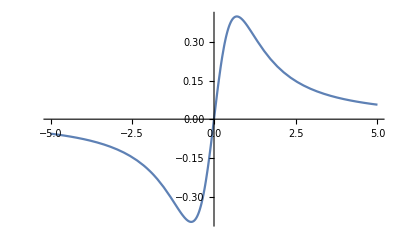

```mathematica
XbTChosenFast[{0,0,0,0,0,0,0,0,10,0,0,1,0,0,0},{0,0,0}]
Plot[XbTChosenFast[{0,0,p,0,0,0,0,0,10,0,0,1,0,0,0},{0,0,0}][[3]],{p,-5,5}]
```

### control law

#### update thrust control law

```mathematica
T2cl[x3_,B_]:=Module[{
x2=x3[[1;;15]],
bT=x3[[16;;18]]
},
T1cl[x2,bT,B]/.Controllers
]
(*test*)
If[!COMMENT,T2cl[x3R[],B/.PhysicalConstants]]
```

#### update angular velocity control law: angular velocity depends on bT and on bTdot, which we designed above

```mathematica
ω2cl[x3_]:=Module[{
x2=x3[[1;;15]],
bT=x3[[16;;18]]
},
Module[{bTdot=Evaluate[XbT[x2,bT]/.Estimators]},
ω1cl[x2,bT,bTdot]/.Controllers
]
]
(*test*)
If[!COMMENT,ω2cl[x3R[]]]
```

```mathematica
(*ω2clA[x3_]:=Module[{
x2=x3[[1;;15]],
bT=x3[[16;;18]]
},
Module[{bTdot=Evaluate[DiagonalMatrix[kibT/.Estimators].XbTChosenFast[x2,bT]/.Estimators]},
ω1cl[x2,bT,bTdot]/.Controllers
]
]
ω2clB[x3_]:=Module[{
x2=x3[[1;;15]],
bT=x3[[16;;18]]
},
Module[{bTdot=Evaluate[EstimatorProj2[DiagonalMatrix[kibT/.Estimators].XbTChosenFast[x2,bT],bT,{θ0bT,ϵbT,δbT,nbT}]/.Estimators]},
ω1cl[x2,bT,bTdot]/.Controllers
]
]
dω2cl[{p1_,p2_,p3_,v1_,v2_,v3_,g01_,g02_,g03_,n1_,n2_,n3_,g11_,g12_,g13_,bT1_,bT2_,bT3_}]=Module[{
bT={bT1,bT2,bT3},
x3={p1,p2,p3,v1,v2,v3,g01,g02,g03,n1,n2,n3,g11,g12,g13,bT1,bT2,bT3}
},
If[(bT.bT-θ0bT^2/.Estimators)≤ 0,
Evaluate[D[ω2clA[x3],{x3}]],
Evaluate[D[ω2clB[x3],{x3}]]
]
];
Timing[dω2cl[x3R[]]]*)
```

### complete control law

```mathematica
u3cl[x3_,g2_,B_]:=Module[{
x2=x3[[1;;15]],
bT=x3[[16;;18]]
},
Join[
{T2cl[x3,B]},(*thrust control law: still depends on B*)
ω2cl[x3],(*angular velocity control law*)
g2(*d/dt g1*)
]
]/.Controllers
(*test*)
If[!COMMENT,u3cl[x3R[],RandomReal[{-2,2},3],B/.PhysicalConstants]]
```

### closed-loop vector field

```mathematica
X3cl[x3_,g2_,b_,B_]:=X3[x3,u3cl[x3,g2,B],b,B]
(*test*)
If[!COMMENT,X3cl[x3R[],RandomReal[{-2,2},3],b,B]/.PhysicalConstants]
```

### check d/dt x_3^eq=(X_(3,b,B))^cl(x_3^eq,g_2)

```mathematica
error[t_]:=x3eq'[t]-X3cl[x3eq[t],g''[t],b/.PhysicalConstants,B/.PhysicalConstants]/.PhysicalConstants
(*test*)
If[!COMMENT,error[RandomReal[]]//Chop]
```

### Lyapunov function V3: for analysis only

```mathematica
(*REMARK*)
(* note that Subscript[V, 2] does not depend on BT though*)
(*V3 is only for analysis purposes*)
Subscript[V, 3][x3_,b_]:=Module[
{
x2=x3[[1;;15]],
bT=x3[[16;;18]]
},
Subscript[V, 2,0] Log[(Subscript[V, 2][x2,bT]+Subscript[V, 2,0])/Subscript[V, 2,0]]+(#.DiagonalMatrix[1/kibT/.Estimators].#&[b-bT])/2/.ControllersWithEstimators
]
(*test*)
If[!COMMENT,Subscript[V, 3][x3R[],b/.PhysicalConstants]]
```

### Lyapunov function time derivative (V̇)_3 along vector field (X_(3,b,B))^cl (for analysis only)

```mathematica
Subscript[W, 3][x3_,b_]:=Module[{
x2=x3[[1;;15]],
bT=x3[[16;;18]]
},
(1+(Subscript[V, 2][x2,bT])/(Subscript[V, 2,0]/.Controllers))^-1 Subscript[W, 2][x2,bT]-(b-bT).DiagonalMatrix[1/kibT/.Estimators].(XbT[x2,bT]-DiagonalMatrix[kibT/.Estimators].XbTChosenFast[x2,bT])/.Estimators
]
(*test*)
If[!COMMENT,Subscript[W, 3][x3R[],b/.PhysicalConstants]]
```

### check "(V̇)_3=W_3"

```mathematica
error[x3_,g2_,b_,B_]:=(Evaluate[D[Subscript[V, 3][#,b],{#}]]/.Thread[#-> x3]&[Array[Subscript[x, #]&,x3Dim]]).X3cl[x3,g2,b,B]-Subscript[W, 3][x3,b]
(*check when Subscript[b, T]=b*)
(*error[Join[x3R[][[1;;-4]],b/.PhysicalConstants],RandomReal[{-2,2},3],b/.PhysicalConstants,B/.PhysicalConstants]/.Controllers//Chop *)
(*check*)
If[!COMMENT,error[x3R[],RandomReal[{-2,2},3],b/.PhysicalConstants,B/.PhysicalConstants]/.Controllers//Chop]
```

## step 4: B unknown

### state

x_4=(x_3,B_T)
x_3 previous state
B_T estimate of B

```mathematica
x4R[]:=Module[{
BT=(#1/(√(#1.#1+#2^2))&[RandomReal[{-#,#},3],#])&[θ0BT+ϵBT/.EstimatorsParameters]
},
Join[x3R[],BT]
];
If[!COMMENT,x4R[]]
x4Dim=Length[x4R[]];
```

### projection

```mathematica
Projx4[x4_]:=Join[Projx3[x4[[1;;18]]],x4[[19;;21]]]
Projx4[#]-#&[x4R[]]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### input

same input as in the previous step
u_2=(T, ω, g_2)
thrust + angular velocity + d/dt g_1

### equilibrium trajectory x_4^eq

```mathematica
x4eq[t_]:=Join[
x3eq[t],(*previous equilibrium trajectory*)
B/.PhysicalConstants
]
(*test*)
If[!COMMENT,x4eq[RandomReal[]]//N]
```

### open-loop vector field

```mathematica
XBT[x3_,BT_]:={XBT1[x3,BT],XBT2[x3,BT],XBT3[x3,BT]}

X4[x4_,u4_,b_,B_]:=Module[{
x3=x4[[1;;18]],(*previous state*)
BT=x4[[19;;21]],(*estimate of disturbance B*)

T=u4[[1]],(*thrust input*)
ω=u4[[2;;4]],(*angular velocity input*)
g2=u4[[5;;7]](*d/dt Subscript[g, 1]*)
},
Join[
X3[x3,Join[{T},ω,g2],b,B],
XBT[x3,BT]/.Estimators
]
]
```

### estimator BT update law

```mathematica
XBTChosenFast[x3_,BT_]:=Module[{
n=x3[[10;;12]],
x2=x3[[1;;15]],
bT=x3[[16;;18]]
},
XbTChosenFast[x2,bT].n ϕT[n]/.Controllers
]
(*test*)
If[!COMMENT,XBT[x3R[],RandomReal[{-2,2},3]]/.ControllersWithEstimators]
```

### update thrust control law

```mathematica
T3cl[x4_]:=Module[{
x3=x4[[1;;-4]],
BT=x4[[-3;;-1]]
},
T2cl[x3,BT]
]
```

### complete control law

```mathematica
u4cl[x4_,g2_]:=Module[{
x3=x4[[1;;18]],
BT=x4[[19;;21]]
},
Join[
{T3cl[x4]},(*thrust control law: no dependence on b or B*)
ω2cl[x3],(*angular velocity control law*)
g2(*d/dt g1*)
]
]/.Controllers
(*test*)
If[!COMMENT,u4cl[x4R[],RandomReal[{-2,2},3]]]
```

### vector field + control law + closed loop (all together)

```mathematica
X4cl[x4_,g2_,b_,B_]:=X4[x4,u4cl[x4,g2],b,B]
(*test*)
If[!COMMENT,X4cl[x4R[],RandomReal[{-2,+2},3],b,B]/.PhysicalConstants]
```

### check d/dt x_4^eq=(X_(4,b,B))^cl(x_4^eq,g_2)

```mathematica
error[t_]:=x4eq'[t]-X4cl[x4eq[t],g''[t],b/.PhysicalConstants,B/.PhysicalConstants]/.PhysicalConstants
(*test*)
error[RandomReal[]]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Lyapunov function V_4: for analysis only

```mathematica
Subscript[V, 4][x4_,b_,B_]:=Module[{
x3=x4[[1;;18]](*p,v,g0,n,g1,bT*),
BT=x4[[19;;21]]
},
Subscript[V, 3][x3,b]+(#.DiagonalMatrix[1/kiBT/.Estimators].#&[B-BT])/2/.Estimators
]
(*test*)
If[!COMMENT,Subscript[V, 4][x4R[],b,B]/.ControllersWithEstimators/.PhysicalConstants]
```

### Lyapunov function time derivative (V̇)_4 along vector field (X_(4,b,B))^cl (for analysis only)

```mathematica
Subscript[W, 4][x4_,b_,B_]:=Module[{
x3=x4[[1;;-4]],
BT=x4[[-3;;-1]]
},
Subscript[W, 3][x3,b]-(B-BT).DiagonalMatrix[1/kiBT/.Estimators].(XBT[x3,BT]-DiagonalMatrix[kiBT/.Estimators]. XBTChosenFast[x3,BT])/.Estimators
]
(*test*)
If[!COMMENT,Subscript[W, 4][x4R[],b/.PhysicalConstants,B/.PhysicalConstants]]
```

### check "(V̇)_4=W_4"

```mathematica
error[x4_,g2_,b_,B_]:=(Evaluate[D[Subscript[V, 4][#,b,B],{#}]]/.Thread[#-> x4]&[Array[Subscript[x, #]&,x4Dim]]).X4cl[x4,g2,b,B]-Subscript[W, 4][x4,b,B]
(*check*)
If[!COMMENT,error[x4R[],RandomReal[{-2,2},3],b/.PhysicalConstants,B/.PhysicalConstants]/.Controllers//Chop]
```

## Simulation

```mathematica
x40=Join[
{5,5,5},(*p*)
{2,2,2},(*v*)
g[0]/.Controllers,(*g0*)
{0,0,1},(*n*)
g'[0]/.Controllers,(*g1*)
{0,0,0},(*bT*)
{0,0,0}(*BT*)
]//N;
x40=Projx4[x40];
```

```mathematica
stepsize=0.01;
TFINAL=35;
NN=Round[35/stepsize];
If[SIMSTEP4,
(*stepsize=0.005;
NN=7000;*)

stateList={};
(*stateListStar={};*)
inputList ={};
(*tensionsList={};*)
VList={};
WList={};
kk=1;
i0=1;
For[i=i0,i<=NN,i++,
time=stepsize(i-1);

input=u4cl[x40,g''[time]/.Controllers];
VF=X4[x40,input,b/.PhysicalConstants,B/.PhysicalConstants]/.PhysicalConstants//N;

stateList= Join[stateList,{x40}];
inputList= Join[inputList,{input}];
VList= Join[VList,{Subscript[V, 4][x40,b,B]/.PhysicalConstants}];
WList= Join[WList,{Subscript[W, 4][x40,b,B]/.PhysicalConstants}];

x40=Projx4[x40+stepsize VF];

If[i≥300 kk,Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*);Print[i];kk=kk+1];
]
]
Play[Sin[440 2Pi t],{t,0,1}]
Play[Sin[440 2Pi t],{t,0,1}]
Play[Sin[440 2Pi t],{t,0,1}]
```

#### continue

```mathematica
(*x40=stateList[[-1,;;]];
i0=i-1;
NN=1600;
stateList=stateList[[1;;-2,;;]];
inputList=inputList[[1;;-2,;;]];

For[i=i0,i<=NN,i++,
time=stepsize(i-1);

input=u4cl[x40,g''[time]/.Controllers];
VF=X4[x40,input,b/.PhysicalConstants,B/.PhysicalConstants]/.PhysicalConstants//N;

stateList= Join[stateList,{x40}];
inputList= Join[inputList,{input}];

x40=Projx4[x40+stepsize VF];

If[i≥100 kk,Beep[];Print[i];kk=kk+1];
]*)
```

### necessary for the plots that follow

```mathematica
NN=Length[stateList];
XTicksLabels=Table[{Round[1/stepsize]i+1,i},{i,0,TFINAL,2}];
```

## Error position

```mathematica
errorp:= stateList[[1;;NN,{1,2,3}]];
If[SIMSTEP4,
Labeled[
ListLinePlot[{
errorp[[;;,1]],errorp[[;;,2]],errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","position error(m)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP4,Export[NotebookDirectory[]<>"figures/step4/error_position.pdf",%];]
```

## Error velocity

```mathematica
errorv:= stateList[[1;;NN,{4,5,6}]];
If[SIMSTEP4,
Labeled[
ListLinePlot[{
errorv[[;;,1]],errorv[[;;,2]],errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","error(m/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP4,Export[NotebookDirectory[]<>"figures/step4/error_velocity.pdf",%];]
```

```mathematica
errorv:= stateList[[1;;NN,{4,5,6}]];
If[SIMSTEP4,
Labeled[
ListLinePlot[{
errorv[[;;,1]],errorv[[;;,2]],errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->{-0.1,0.1}
],
{"time (s)","error(m/s)"},{Bottom,Left},RotateLabel->True
]
]
```

## Disturbance estimates

```mathematica
estimate[i_]:= stateList[[i,{16,17,18,19,20,21}]];
```

### disturbance bT

```mathematica
If[SIMSTEP4,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]],{i,1,NN}],
Table[estimate[i][[2]],{i,1,NN}],
Table[estimate[i][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate b_T(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP4,Export[NotebookDirectory[]<>"figures/step4/bT.pdf",%];]
```

#### note that b != bT

```mathematica
b/.PhysicalConstants
If[SIMSTEP4,√(#.#)&[b-estimate[-1][[1;;3]]/.PhysicalConstants]]
If[SIMSTEP4,180/π ArcCos[(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-b]).(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-estimate[-1][[1;;3]]])]/.PhysicalConstants]
```

{0.212132,0.,-0.212132}

### disturbance BT

```mathematica
If[SIMSTEP4,
Labeled[
ListLinePlot[{
Table[estimate[i][[4]],{i,1,NN}],
Table[estimate[i][[5]],{i,1,NN}],
Table[estimate[i][[6]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate B_T(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP4,Export[NotebookDirectory[]<>"figures/step4/BBT.pdf",%];]
```

#### note that B != BT

```mathematica
B/.PhysicalConstants
If[SIMSTEP4,√(#.#)&[B-estimate[-1][[4;;6]]/.PhysicalConstants]]
If[SIMSTEP4,#1.#2&[B-estimate[-1][[4;;6]],ϕT[stateList[[-1,{10,11,12}]]] ]/.PhysicalConstants]
```

{-0.012132,0.2,0.312132}

```mathematica
If[SIMSTEP4,
Module[
{
b=b/.PhysicalConstants,
B=B/.PhysicalConstants,
bT=estimate[-1][[1;;3]],
BT=estimate[-1][[4;;6]],
n=stateList[[-1,{10,11,12}]]
},
b-bT+(ϕT[n]/.PhysicalConstants).(B-BT)n
]
]
```

## Input

```mathematica
If[SIMSTEP4,
Labeled[
ListLinePlot[{
inputList[[;;,1]]
},
PlotLegends->Placed[{"Thrust input"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(m/s/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP4,Export[NotebookDirectory[]<>"figures/step4/thrust_input.pdf",%];]
If[SIMSTEP4,
Labeled[
ListLinePlot[{
inputList[[;;,2]],
inputList[[;;,3]],
inputList[[;;,4]]
},
PlotLegends->Placed[{"ω_1","ω_2","ω_3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","Angular velocity (rad/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP4,Export[NotebookDirectory[]<>"figures/step4/angular_velocity_input.pdf",%];]
```

## Lyapunov function

```mathematica
If[SIMSTEP4,
Labeled[
ListLinePlot[{
(*Table[Subscript[V, 4][stateList[[i]],b,B]/.PhysicalConstants,{i,1,Length[stateList]}],*)
(*Table[-Subscript[W, 4][stateList[[i]],b,B]/.PhysicalConstants,{i,1,Length[stateList]}]*)
VList,
WList
},
PlotLegends->Placed[{"V_4","W_4"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(m/s/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP4,Export[NotebookDirectory[]<>"figures/step4/lyapunov_and_derivative.pdf",%];]
```

# Steps 5 to 6: control at angular acceleration level

## step 5: torque control (assuming (b,B) are know)

we don' t have control over the angular velocity ω, like in step 4

### state

x_5=(x_4,ω,g_2)
x_4 previous state
ω angular velocity
g_2=d/dt g_1

```mathematica
x5R[]:=Join[#,OP[#[[10;;12]]].(RandomReal[{-1,1},3]),RandomReal[{-2,2},3]]&[x4R[]];
If[!COMMENT,x5R[]]
x5Dim=Length[x5R[]];
```

### projection

```mathematica
Projx5[x5_]:=Join[Projx4[x5[[1;;21]]],OP[x5[[10;;12]]].x5[[22;;24]],x5[[25;;27]]]
Projx5[#]-#&[x5R[]]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### input

u_5=(T, τ, g_3)
thrust + angular acceleration + d/dt g_2

### equilibrium trajectory x_5^eq: FIX dependence on controllers

```mathematica
x5eq[t_]:=Join[
x4eq[t],(*previous equilibrium trajectory*)
Skew[#1/(√(#1.#1))].(#2/(√(#1.#1)))&[g[t]-(b/.PhysicalConstants),g'[t]-{0,0,0}],
g''[t]
]/.Controllers
(*test*)
If[!COMMENT,x5eq[RandomReal[]]//N]
```

### vector field

```mathematica
X5[x5_,u5_,b_,B_]:=Module[{
n=x5[[10;;12]],
x4= x5[[1;;21]],
ω = x5[[22;;24]],
g2 = x5[[25;;27]],

T=u5[[1]],
τ=u5[[2;;4]],
g3=u5[[5;;7]]
},
Join[
X4[x4,Join[{T},ω,g2],b,B],
OP[n].(τ+ϕτ[n].B),
g3
]
]
(*test*)
If[!COMMENT,X5[x5R[],{1,2,3,4,5,6,7},b,B]/.PhysicalConstants]
```

### estimator: none

```mathematica
τ1cl[x5_,b_,B_]:=Module[{
p=x5[[1;;3]],
v=x5[[4;;6]],

g0=x5[[7;;9]],
n=x5[[10;;12]],

bT=x5[[16;;18]],
BT=x5[[19;;21]],
ω=x5[[22;;24]],
g2=x5[[25;;27]],

x2=x5[[1;;15]],
x3=x5[[1;;18]],
x4=x5[[1;;21]]
},
Module[{
d0uDI=Evaluate[uDIChosen[p,v]],

ω0d=Evaluate[ω2cl[x3]],
(*dω=Evaluate[dω2cl[x3]],*)
dω=Transpose[Table[D[ω2cl[ReplacePart[x3,i->x]],x]/.{x->x3[[i]] },{i,Range[18]}]],

VV=Evaluate[Subscript[V, 2][x2,bT]]

},
Module[{
ω1d=Evaluate[dω.X3[x3,Join[{T3cl[x4]},ω,g2],b,B]/.Controllers],
 y0d=Evaluate[g0+d0uDI-bT]
},
Module[{
(*∂/(∂n)Subscript[V, 2][x2,bT]*)
dVV=Evaluate[(γθ/.Controllers) ((y0d/(√(y0d.y0d))).Skew[n])]
},
(*NOTE: ω0d is orthogonal to n, but ω1d is not necessarily*)
AngularAcceleration[
ω(*angular velocity*),
{ω0d,OP[n].ω1d}(*desired angular velocity and its time derivative*),
{VV,dVV}/.Controllers,
{kpω,γω,Subscript[V, 2,0]}/.Controllers
]+OP[n].(-ϕτ[n].B)/.Controllers
]
]
]
]
(*test*)
If[!COMMENT,Timing[τ1cl[x5R[],b/.PhysicalConstants,B/.PhysicalConstants]]]
```

### complete control law

```mathematica
u5cl[x5_,g3_,b_,B_]:=Module[{
x4=x5[[1;;-7]]
},
Join[
{T3cl[x4]/.Controllers},
τ1cl[x5,b,B],
g3
]
]
(*test*)
If[!COMMENT,u5cl[x5R[],RandomReal[{-2,2},3],b/.PhysicalConstants,B/.PhysicalConstants]]
```

### vector field + control law (all together)

```mathematica
X5cl[x5_,g3_,b_,B_]:=X5[x5,u5cl[x5,g3,b,B],b,B]
(*test*)
If[!COMMENT,X5cl[x5R[],RandomReal[{-2,+2},3],b,B]/.PhysicalConstants]
```

### check d/dt x_5^eq=(X_(5,b,B))^cl(x_5^eq,g_3)

```mathematica
error[t_]:=x5eq'[t]-X5cl[x5eq[t],g'''[t]/.Controllers,b/.PhysicalConstants,B/.PhysicalConstants]/.PhysicalConstants
(*test*)
If[!COMMENT,error[RandomReal[]]//Chop]
```

### Lyapunov function V_5 (for analysis only)

```mathematica
Subscript[V, 5][x5_,b_,B_]:=Module[{
x3=x5[[1;;18]],
x4=x5[[1;;21]],
ω=x5[[22;;24]]
},
(*(*a: checked*)Subscript[V, 4][x4,b,B]*)
(*(#.#)/2&[ω-ω2cl[x3]]*)
Subscript[V, 4][x4,b,B]+γω ((#.#)/2&[ω-ω2cl[x3]])/.Controllers
]
(*test*)
If[!COMMENT,Subscript[V, 5][x5R[],b,B]/.PhysicalConstants]
```

### Lyapunov function time derivative (V̇)_5 along vector field (X_(5,b,B))^cl (for analysis only)

```mathematica
(*T3dF[x3_]:=Module[{
p=x3[[1;;3]],
v=x3[[4;;6]],
g0=x3[[7;;9]],
(*n=x3[[10;;12]],*)
(*g1=x3[[13;;15]],*)
bT=x3[[16;;18]]
},
Evaluate[g0+Evaluate[uDIChosen[p,v]]-bT]
]*)
```

```mathematica
Subscript[W, 5][x5_,b_,B_]:=Module[{
x2=x5[[1;;15]],
bT=x5[[16;;18]],
x3=x5[[1;;18]],
x4=x5[[1;;-7]],
ω=x5[[-6;;-4]],
n=x5[[10;;12]]
},
(*(*a: CORRECT*)Subscript[W, 4][x4,b,B]+(1+(Subscript[V, 2][x2,bT])/Subscript[V, 2,0])^-1 γθ (#/(√(#.#))&[T3dF[x3]]).Skew[n].(ω-ω2cl[x3])/.Controllers*)
(*(ω-ω2cl[x3]).(τ1cl[x5,b,B])/.Controllers*)
Subscript[W, 4][x4,b,B]-(kpω γω/.Controllers) (#.#&[ω-ω2cl[x3]])/.Controllers/.Estimators
]
(*test*)
If[!COMMENT,Subscript[W, 5][x5R[],b/.PhysicalConstants,B/.PhysicalConstants]]
```

### check "(V̇)_5=W_5"

```mathematica
x5Rexample=x5R[];
```

```mathematica
error[x5_,g3_,b_,B_]:=Evaluate[Array[D[Subscript[V, 5][ReplacePart[x5,#->x],b,B],x]/.{x->x5[[#]] }&,27]].X5cl[x5,g3,b,B]-Subscript[W, 5][x5,b,B]
(*check*)
If[!COMMENT,error[x5Rexample,RandomReal[{-2,2},3],b/.PhysicalConstants,B/.PhysicalConstants]/.Controllers//Chop]
```

0

```mathematica
(*approximation*)
error[x5_,g3_,b_,B_]:=((Subscript[V, 5][Evaluate[Projx5[x5+Δt #]],b,B]-Subscript[V, 5][x5,b,B])/Δt/.PhysicalConstants/.{Δt->0.0005Min[1,1/Norm[#]]})&[Evaluate[X5cl[x5,g3,b,B]/.PhysicalConstants]] -Subscript[W, 5][x5,b,B]
(*check*)
If[!COMMENT,error[x5Rexample,RandomReal[{-2,2},3],b/.PhysicalConstants,B/.PhysicalConstants]/.Controllers//Chop]
```

## step 6: b and B not know by torque control law

### state

x_6=(x_5,b_τ,B_τ)
x_5 previous state
b_τ estimate of disturbance b
B_τ estimate of disturbance B

```mathematica
x6R[]:=Module[{
bτ=(#1/(√(#1.#1+#2^2))&[RandomReal[{-#,#},3],#])&[θ0bτ+ϵbτ/.EstimatorsParameters],
Bτ=(#1/(√(#1.#1+#2^2))&[RandomReal[{-#,#},3],#])&[θ0Bτ+ϵBτ/.EstimatorsParameters]
},
Join[x5R[],bτ,Bτ]
];
If[!COMMENT,x6R[]]
x6RDim=Length[x6R[]];
```

### projection

```mathematica
Projx6[x6_]:=Join[Projx5[x6[[1;;27]]],x6[[28;;33]]]
Projx6[#]-#&[x6R[]]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### input

same input as before
u_6=u_5=(T, τ, g_3)
thrust + angular acceleration + d/dt g_2

### open-loop vector field

#### generic form of estimators

```mathematica
Xbτ[x5_,bτ_]:={Xbτ1[x5,bτ],Xbτ2[x5,bτ],Xbτ3[x5,bτ]}
XBτ[x5_,Bτ_]:={XBτ1[x5,Bτ],XBτ2[x5,Bτ],XBτ3[x5,Bτ]}
```

```mathematica
X6[x6_,u6_,b_,B_]:=Module[{
x5=x6[[1;;27]],(*previous state*)
bτ=x6[[28;;30]],(*estimate of disturbance b*)
Bτ=x6[[31;;33]],(*estimate of disturbance B*)

u5=u6
},
Join[
X5[x5,u5,b,B],
Xbτ[x5,bτ]/.Estimators,
XBτ[x5,Bτ]/.Estimators
]
]
(*test*)
(*If[!COMMENT,X6[x6R[],RandomReal[{-2,2},7],b/.PhysicalConstants,B/.PhysicalConstants]/.PhysicalConstants]*)
```

### Lyapunov function time derivative (V̇)_5 along vector field X_(5,b,B)(x_5,(T_3^cl(x_4),τ_1^cl(x_5,b_τ,B_τ),g^3 ))

```mathematica
Subscript[WModified, 5][x5_,b_,B_,bτ_,Bτ_]:=Module[{
x2=x5[[1;;15]](*p,v,g0,n,g1*),
x3=x5[[1;;18]](*p,v,g0,n,g1,bT*),
x4=x5[[1;;21]],
bT=x5[[16;;18]],
BT=x5[[19;;21]],
ω=x5[[22;;24]],

n=x5[[10;;12]]
},
Module[{
dvω2cl=Transpose[Table[D[ω2cl[ReplacePart[x3,i->x]],x]/.{x->x3[[i]] },{i,{4,5,6}}]]
(*dvω2cl=Evaluate[dω2cl[x3]][[;;,{4,5,6}]]*)
},
Subscript[W, 5][x5,b,B]+γω (ω-ω2cl[x3]).(OP[n].ϕτ[n].(B-Bτ)-dvω2cl.((b-bτ) + ϕT[n].(B-Bτ)n))/.ControllersWithEstimators
]
]
(*test*)
If[!COMMENT,Subscript[WModified, 5][x5R[],b/.PhysicalConstants,B/.PhysicalConstants,RandomReal[{-2,2},3],RandomReal[{-2,2},3]]]
```

```mathematica
error[x5_,g3_,b_,B_,bτ_,Bτ_]:=Evaluate[Array[D[Subscript[V, 5][ReplacePart[x5,#->x],b,B],x]/.{x->x5[[#]] }&,x5Dim]].(X5[x5,u5cl[x5,g3,bτ,Bτ],b,B]/.PhysicalConstants)-Subscript[WModified, 5][x5,b,B,bτ,Bτ]
If[!COMMENT,
error[x5R[],RandomReal[{-2,2},3],b/.PhysicalConstants,B/.PhysicalConstants,RandomReal[{-2,2},3],RandomReal[{-2,2},3]]//Chop
]
```

0

### Estimators for bτ and Bτ

```mathematica
XbτChosenFast[x5_,bτ_]:=Module[{
n=x5[[10;;12]],
ω=x5[[22;;24]],
x3=x5[[1;;18]]
},
Module[{
ωcl=ω2cl[x3],
dvω2cl=Transpose[Table[D[ω2cl[ReplacePart[x3,i->x]],x]/.{x->x3[[i]] },{i,{4,5,6}}]]
},
(*projection not necessary because ω and ωcl are orthogonal to n*)
γω(ω-ωcl).(-dvω2cl)/.Controllers
]
]
XBτChosenFast[x5_,Bτ_]:=Module[{
n=x5[[10;;12]],
ω=x5[[22;;24]],
x3=x5[[1;;18]]
},
Module[{
ωcl=ω2cl[x3],
dvω2cl=Transpose[Table[D[ω2cl[ReplacePart[x3,i->x]],x]/.{x->x3[[i]] },{i,{4,5,6}}]]
},
(*projection not necessary because ω and ωcl are orthogonal to n*)
γω(ω-ωcl).(ϕτ[n]-KroneckerProduct[dvω2cl.n, ϕT[n]])/.Controllers
]
]
```

```mathematica
If[!COMMENT,XbτChosenFast[x5R[],RandomReal[{-2,2},3]]//Timing]
If[!COMMENT,XBτChosenFast[x5R[],RandomReal[{-2,2},3]]//Timing]
```

{1.504,{-27.0755,22.482,19.0849}}

{1.74,{42.2456,23.9244,-21.6502}}

### update torque control law

```mathematica
τ2cl[x6_]:=Module[{
x5=x6[[1;;-7]],
bτ=x6[[28;;30]],
Bτ=x6[[31;;33]]
},
τ1cl[x5,bτ,Bτ]
]
(*test*)
If[!COMMENT,τ2cl[x6R[]]//Timing]
```

{3.62,{4.42602,25.1969,3.31987}}

### complete control law

```mathematica
u6cl[x6_,g3_]:=Module[{
x4=x6[[1;;21]]
},
Join[
{T3cl[x4]},
τ2cl[x6],
g3
]
]/.Controllers
(*test*)
If[!COMMENT,u6cl[x6R[],RandomReal[{-2,2},3]]]//Timing
```

{3.624,{-2.39565,0.766803,2.46479,-9.37136,0.500213,-0.480023,0.693971}}

### vector field + control law + closed loop (all together)

```mathematica
X6cl[x6_,g3_,b_,B_]:=X6[x6,u6cl[x6,g3],b,B]
(*test*)
If[!COMMENT,X6cl[x6R[],RandomReal[{-2,2},3],b,B]/.PhysicalConstants]//Timing
```

{13.592,{-0.761381,0.463161,0.950169,0.0162931,1.25063,-2.79452,-0.107448,0.656625,-0.220967,-0.130972,-0.257811,-0.146281,-0.339412,1.51103,-1.95459,-0.47458,0.865863,0.242347,0.736888,-0.393573,0.511944,0.233429,5.99627,2.94576,-1.91898,1.2109,-1.93063,-1.0425,-0.930743,-0.581458,-0.962552,-0.618312,-0.199713}}

### Lyapunov function V_6

```mathematica
Subscript[V, 6][x6_,b_,B_]:=Module[{
bT=x6[[16;;18]],
BT=x6[[19;;21]],
x3=x6[[1;;18]],
x4=x6[[1;;21]],
ω=x6[[22;;24]],
x5=x6[[1;;27]](*p,v,g0,n,g1,bT,BT,ω,g2*),
bτ=x6[[28;;30]],
Bτ=x6[[31;;33]]
},
(*Subscript[V, 5][x5,b,B]/.ControllersWithEstimators*)
 Subscript[V, 5][x5,b,B]+(#.#&[b-bτ])/(2 kibτ)+(#.#&[B-Bτ])/(2 kiBτ)/.ControllersWithEstimators
]
(*test*)
If[!COMMENT,Subscript[V, 6][x6R[],b,B]/.PhysicalConstants]
```

35.8669

### Lyapunov function time derivative (V̇)_6 along vector field (X_(6,b,B))^cl (for analysis only)

```mathematica
Subscript[W, 6][x6_,b_,B_]:=Module[{
x2=x6[[1;;15]](*p,v,g0,n,g1*),
x3=x6[[1;;18]](*p,v,g0,n,g1,bT*),
x4=x6[[1;;21]],
bT=x6[[16;;18]],
BT=x6[[19;;21]],
ω=x6[[22;;24]],
x5=x6[[1;;27]](*p,v,g0,n,g1,bT,BT,ω,g2*),
bτ=x6[[28;;30]],
Bτ=x6[[31;;33]],
n=x6[[10;;12]]
},
Module[{
dvω2cl=Transpose[Table[D[ω2cl[ReplacePart[x3,i->x]],x]/.{x->x3[[i]] },{i,{4,5,6}}]]
(*dvω2cl=Evaluate[dω2cl[x3]][[;;,{4,5,6}]]*)
},
(*Subscript[W, 5][x5,b,B]+(b-bτ).XbτChosenFast[x5,bτ]+(B-Bτ). XBτChosenFast[x5,Bτ]/.ControllersWithEstimators*)
Subscript[W, 5][x5,b,B]-((b-bτ).(Xbτ[x5,bτ]-kibτ XbτChosenFast[x5,bτ]))/kibτ-((B-Bτ).(XBτ[x5,Bτ]-kiBτ XBτChosenFast[x5,Bτ]))/kiBτ/.ControllersWithEstimators
]
]
(*test*)
If[!COMMENT,Subscript[W, 6][x6R[],b/.PhysicalConstants,B/.PhysicalConstants]]
```

-157.417

### check "(V̇)_6=W_6"

```mathematica
error[x6_,g3_,b_,B_]:=Evaluate[Array[D[Subscript[V, 6][ReplacePart[x6,#->x],b,B],x]/.{x->x6[[#]] }&,33]].(X6cl[x6,g3,b,B]/.PhysicalConstants)-Subscript[W, 6][x6,b,B]
(*check*)
(*error[Join[x6R[][[1;;-7]],#1,#2],RandomReal[{-2,2},3],#1,#2]&[b/.PhysicalConstants,B/.PhysicalConstants]//Chop*)
If[!COMMENT,
error[x6R[],RandomReal[{-2,2},3],b/.PhysicalConstants,B/.PhysicalConstants]//Chop
]
```

0

## Simulation

```mathematica
x60=Join[
{10,10,10},(*p*)
{2,2,2},(*v*)
g[0]/.Controllers,(*g0*)
{0,0,1},(*n*)
g'[0]/.Controllers,(*g1*)
{0,0,0},(*bT*)
{0,0,0},(*BT*)
{0,0,0}(*ω*),
g''[0]/.Controllers(*g2*),
{0,0,0}(*bτ*),
{0,0,0}(*Bτ*)
]//N;
```

```mathematica
stepsize=0.01;
TFINAL=10;
NN=Round[10/stepsize];
If[SIMSTEP6,
stepsize=0.01;

stateList={};
(*stateListStar={};*)
inputList ={};
(*tensionsList={};*)
VList ={};
WList ={};
kk=1;
i0=1;
For[i=i0,i<=NN,i++,
time=stepsize(i-1);

input=u6cl[x60,g'''[time]/.Controllers];

VF=X6[x60,input,b/.PhysicalConstants,B/.PhysicalConstants]/.PhysicalConstants//N;

stateList= Join[stateList,{x60}];
inputList= Join[inputList,{input}];
VList= Join[VList,{Subscript[V, 6][x60,b,B]/.PhysicalConstants}];
WList= Join[WList,{Subscript[W, 6][x60,b,B]/.PhysicalConstants}];

x60=Projx6[x60+stepsize VF];

If[i≥100 kk,Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*);Print[i];kk=kk+1];
]
]
```

### necessary for the plots that follow

```mathematica
NN=Length[stateList];
XTicksLabels=Table[{Round[1/stepsize]i+1,i},{i,0,TFINAL,2}];
```

## Error position

```mathematica
errorp:= stateList[[1;;NN,{1,2,3}]];
If[SIMSTEP6,
Labeled[
ListLinePlot[{
errorp[[;;,1]],errorp[[;;,2]],errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","position error(m)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP6,Export[NotebookDirectory[]<>"figures/step6/error_position.pdf",%];]
```

## Error velocity

```mathematica
errorv:= stateList[[1;;NN,{4,5,6}]];
If[SIMSTEP6,
Labeled[
ListLinePlot[{
errorv[[;;,1]],errorv[[;;,2]],errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","error(m/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP6,Export[NotebookDirectory[]<>"figures/step6/error_velocity.pdf",%];]
```

## Disturbance estimates

```mathematica
estimate[i_]:= stateList[[i,{16,17,18,19,20,21}]];
```

### disturbance bT

```mathematica
If[SIMSTEP6,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]],{i,1,NN}],
Table[estimate[i][[2]],{i,1,NN}],
Table[estimate[i][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate b_T(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP6,Export[NotebookDirectory[]<>"figures/step6/bT.pdf",%];]
```

#### note that b != bT

```mathematica
b/.PhysicalConstants
If[SIMSTEP6,√(#.#)&[b-estimate[-1][[1;;3]]/.PhysicalConstants]]
If[SIMSTEP6,180/π ArcCos[(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-b]).(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-estimate[-1][[1;;3]]])]/.PhysicalConstants]
```

{0.212132,0.,-0.212132}

### disturbance BT

```mathematica
If[SIMSTEP6,
Labeled[
ListLinePlot[{
Table[estimate[i][[4]],{i,1,NN}],
Table[estimate[i][[5]],{i,1,NN}],
Table[estimate[i][[6]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate B_T(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP6,Export[NotebookDirectory[]<>"figures/step6/BBT.pdf",%];]
```

#### note that b != bT

```mathematica
B/.PhysicalConstants
If[SIMSTEP6,√(#.#)&[B-estimate[-1][[4;;6]]/.PhysicalConstants]]
If[SIMSTEP6,#1.#2&[B-estimate[-1][[4;;6]],ϕT[stateList[[-1,{10,11,12}]]] ]/.PhysicalConstants]
```

{-0.012132,0.2,0.312132}

## Disturbance estimates

```mathematica
estimate[i_]:= stateList[[i,{28,29,30,31,32,33}]];
```

### disturbance bτ

```mathematica
If[SIMSTEP6,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]],{i,1,NN}],
Table[estimate[i][[2]],{i,1,NN}],
Table[estimate[i][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate b_τ(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP6,Export[NotebookDirectory[]<>"figures/step6/btau.pdf",%];]
```

#### note that b != bτ

```mathematica
b/.PhysicalConstants
If[SIMSTEP6,√(#.#)&[b-estimate[-1][[1;;3]]/.PhysicalConstants]]
If[SIMSTEP6,180/π ArcCos[(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-b]).(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-estimate[-1][[1;;3]]])]/.PhysicalConstants]
```

{0.212132,0.,-0.212132}

### disturbance Bτ

```mathematica
If[SIMSTEP6,
Labeled[
ListLinePlot[{
Table[estimate[i][[4]],{i,1,NN}],
Table[estimate[i][[5]],{i,1,NN}],
Table[estimate[i][[6]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate B_τ(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP6,Export[NotebookDirectory[]<>"figures/step6/BBtau.pdf",%];]
```

#### note that B != Bτ

```mathematica
B/.PhysicalConstants
If[SIMSTEP6,√(#.#)&[B-estimate[-1][[4;;6]]/.PhysicalConstants]]
If[SIMSTEP6,#1.#2&[B-estimate[-1][[4;;6]],ϕT[stateList[[-1,{10,11,12}]]] ]/.PhysicalConstants]
```

{-0.012132,0.2,0.312132}

## Input

```mathematica
If[SIMSTEP6,
Labeled[
ListLinePlot[{
inputList[[;;,1]]
},
PlotLegends->Placed[{"Thrust input"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(m/s/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP6,Export[NotebookDirectory[]<>"figures/step6/thrust_input.pdf",%];]
If[SIMSTEP6,
Labeled[
ListLinePlot[{
inputList[[;;,2]],
inputList[[;;,3]],
inputList[[;;,4]]
},
PlotLegends->Placed[{"τ_1","τ_2","τ_3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","Angular acceleration (rad/s/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP6,Export[NotebookDirectory[]<>"figures/step6/angular_acceleration_input.pdf",%];]
```

## Lyapunov function

```mathematica
If[SIMSTEP4,
Labeled[
ListLinePlot[{
(*Table[Subscript[V, 6][stateList[[i]],b,B]/.PhysicalConstants,{i,1,Length[stateList]}],*)
(*Table[-Subscript[W, 6][stateList[[i]],b,B]/.PhysicalConstants,{i,1,Length[stateList]}]*)
VList,
WList
},
PlotLegends->Placed[{"V_6","W_6"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(m/s/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMSTEP4,Export[NotebookDirectory[]<>"figures/step4/lyapunov_and_derivative.pdf",%];]
```